## Initialization

```mathematica
Unprotect["Global`*"]
Clear["Global`*"]
ClearAll["Global`*"] 
Remove["Global`*"] 
<<Notation`
Off[Symbolize::bsymbexs]
Off[Remove::rmnsm]
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]])
Print["Variable Cleared"]
AutoCollapse[]
```

{}

Remove::rmnsm: There are no symbols matching "Global`*".

Variable Cleared

```mathematica
Symbolize[Subscript[u, ρ]]; Symbolize[Subscript[u, ϕ]]; Symbolize[Subscript[u, ζ]]; 
Symbolize[Subscript[u, a]^ρ];Symbolize[Subscript[u, a]^ϕ];Symbolize[Subscript[u, a]^ζ];
Symbolize[u^ρ]; Symbolize[u^ϕ]; Symbolize[u^ζ];
Symbolize[w^ρ]; Symbolize[w^ϕ]; Symbolize[w^ζ];
Symbolize[Subscript[w, ρ]]; Symbolize[Subscript[w, ϕ]]; Symbolize[Subscript[w, ζ]];
 Symbolize[N^𝔄]Symbolize[N^𝔅]Symbolize[N^ℭ];Symbolize[N^𝔇]Symbolize[N^𝔈]Symbolize[N^𝔉];
Symbolize[(U⃗)_n];Symbolize[(X⃗)_r];Symbolize[(U⃗)^n];Symbolize[X⃗];Symbolize[τ^n];
Symbolize[Subscript[a, ρ,𝔄]];Symbolize[Subscript[a, ϕ,𝔅]];Symbolize[Subscript[a, ζ,ℭ]];
Symbolize[Subscript[b, ρ,𝔇]];Symbolize[Subscript[b, ϕ,𝔈]];Symbolize[Subscript[b, ζ,𝔉]]
Symbolize[L̄];
 Notation[g_(i_·j_·)   ⟺  CoVarMetricCoeffs[[i_,j_]]]
Notation[g^(i_·j_·)   ⟺  ContraVarMetricCoeffs[[i_,j_]]]
Notation[Γ_(i_·j_·)^(k_·)   ⟺  Γ[[i_,j_,k_]]]
Notation[w^(i_·)   ⟺  ContraVarDispW[[i_]]]
Notation[u^(i_·)   ⟺  ContraVarDispU[[i_]]]
Notation[u_(i_·)   ⟺  CoVarDispU[[i_]]]
Notation[x^(i_·)   ⟺  Coords[[i_]]]
Notation[w_(j_·)   ⟺  CoVarDispW[[j_]]]
Notation[u^(i_·)|_(j_·)  ⟺  CovariantDU1[i_,j_]]
Notation[u_(i_·)|_(j_·)  ⟺  CovariantDU2[i_,j_]]
Notation[w^(i_·)|_(j_·)  ⟺  CovariantDW1[i_,j_]]
Notation[w_(i_·)|_(j_·)  ⟺  CovariantDW2[i_,j_]]
Notation[γ_(i_·j_·)   ⟺  StrainCovariantU[[i_,j_]]]
Notation[ϵ_(i_·j_·)   ⟺  StrainCovariantW[[i_,j_]]]
Notation[𝔼^(i_·j_·k_·l_·)   ⟺  StiffnessContra[[i_,j_,k_,l_]]]
Notation[(∂u_)/(∂x_)   ⟺  D[u_,x_]]
Notation[τ^(i_·j_·)   ⟺  StressContra[[i_,j_]]]
Symbolize[x_^h];Symbolize[x_^e];
Symbolize[Subscript[U, 1]^n];Symbolize[Subscript[U, 2]^n];Symbolize[Subscript[U, 3]^n]
Symbolize[Subscript[U, n]^1];Symbolize[Subscript[U, n]^2];Symbolize[Subscript[U, n]^3]
Symbolize[Subscript[u, ρ]^h];Symbolize[Subscript[u, ϕ]^h];Symbolize[Subscript[u, ζ]^h]
Symbolize[Subscript[η, g]];Symbolize[Subscript[n, x_]];
Symbolize[N^(i_)];Symbolize[N_(,x_)^(i_)];Symbolize[Subscript[x_, i_]];Symbolize[(x⃗)^h];
Symbolize[Subscript[u, ρ]^h];Symbolize[Subscript[u, ϕ]^h];Symbolize[Subscript[u, ζ]^h];
Symbolize[(f⃗)_(e,a)]
Symbolize[(J^e)^-1];
Symbolize[x̲];
Print["New Symbols Defined"]
AutoCollapse[]
```

New Symbols Defined

```mathematica
<<HaneeshPackages`
PrntRls={Subscript[u, 1]-> Subscript[u,1],Subscript[u, 2]-> Subscript[u,2],Subscript[u, 3]-> Subscript[u,3],
Subscript[x, 1]-> Subscript[x,1],Subscript[x, 2]-> Subscript[x,2],Subscript[x, 3]-> Subscript[x,3],
u^ρ-> Superscript[u,ρ],u^ϕ-> Superscript[u,ϕ],u^ζ-> Superscript[u,ζ],
Subscript[u, ρ]-> Subscript[u,ρ],Subscript[u, ϕ]-> Subscript[u,ϕ],Subscript[u, ζ]-> Subscript[u,ζ],
N^𝔄-> Superscript[N,𝔄],N^𝔅-> Superscript[N,𝔅],N^ℭ-> Superscript[N,ℭ],
N^𝔇-> Superscript[N,𝔇],N^𝔈-> Superscript[N,𝔈],N^𝔉-> Superscript[N,𝔉],N^(a)-> Superscript[N,"(a)"],N^(b)-> Superscript[N,"(b)"],
Subscript[a, ρ, 𝔄]-> Subscript[a,ρ,𝔄],Subscript[a, ϕ, 𝔅]-> Subscript[a,ϕ,𝔅],Subscript[a, ζ, ℭ]-> Subscript[a,ζ,ℭ],
Subscript[b, ρ, 𝔇]-> Subscript[b,ρ,𝔇],Subscript[b, ϕ, 𝔈]-> Subscript[b,ϕ,𝔈],Subscript[b, ζ, 𝔉]-> Subscript[b,ζ,𝔉],N_(,ζ)^(a)->Subsuperscript[N,",ζ","(a)"],N_(,ρ)^(a)->Subsuperscript[N,",ρ","(a)"],N_(,ζ)^(b)->Subsuperscript[N,",ζ","(b)"],N_(,ρ)^(b)->Subsuperscript[N,",ρ","(b)"],
Subscript[w, ρ]-> Subscript[w,ρ],Subscript[w, ϕ]-> Subscript[w,ϕ],Subscript[w, ζ]-> Subscript[w,ζ],
L̄->Overscript[L,_],Subscript[ΔT, 0]-> Subscript[ΔT,0]
};
GenerateMonoSubSuperscriptRules[]:=Module[{body, ww,zz,xx,yy,Prules1,Prules2,scripts},
body=Join[Alphabet["Greek"],Alphabet[],ToUpperCase[Alphabet[]],ToUpperCase[Alphabet["Greek"]]];
scripts=Join[Table[ToString[i],{i,1,9}],List@ToString[ϕ],Map[ToString,Alphabet["Greek"]]];
xx=Flatten@Outer[StringJoin,Map[ToString,body],{"⎵Subscript⎵"},scripts];
xx=Map[Symbol,xx];
yy=Flatten@Outer[Subscript,body,scripts];
Prules1=Table[xx[[i]]->yy[[i]],{i,1,Length@xx}];
ww=Flatten@Outer[StringJoin,Map[ToString,body],{"⎵Superscript⎵"},scripts];
ww=Map[Symbol,ww];
zz=Flatten@Outer[Superscript,body,scripts];
Prules2=Table[ww[[i]]->zz[[i]],{i,1,Length@xx}];
Join[Prules1,Prules2]]
(*PrntRls=Join[PrntRls,GenerateMonoSubSuperscriptRules[]];*)
Pprint[expri_]:=Module[{expr=expri},
expr/.PrntRls//MatrixForm//pdConv
];
Pprint[expri_,title_]:=Module[{expr=expri},
(title=expr)/.PrntRls//MatrixForm//pdConv
];
Print["Print Subroutines Defined"]
AutoCollapse[]
```

Print Subroutines Defined

```mathematica
Subscript[u, ρ]::usage="Covariant component of the displacement in the g^ρ direction (symbol)";
Subscript[u, ϕ]::usage="Covariant component of the displacement in the g^ϕ direction ";
Subscript[u, ζ]::usage="Covariant component of the displacement in the g^ζ direction ";

λ::usage="Lame constant (double)";
μ::usage="Lame constant (double)";
Subscript[ρ, 0]::usage="inner radius (double)";
Subscript[ρ, 1]::usage="outer radius (double)";
Subscript[ζ, 0]::usage="curvilinear coordinate ζ's lower bound(double)";
Subscript[ζ, 1]::usage="curvilinear coordinate ζ's upper bound(double)";
αΔT::usage="α=Coefficient of thermal expansion; ΔT=Temperature change function";

Subscript[n, el]::usage="\tNumber of Finite Elements";
Subscript[n, np]::usage="Number of Finite Element Nodes";
Subscript[n, dof]::usage="Number of degrees of freedom per node";
Subscript[n, en]::usage="Number of nodes per finite element";
Subscript[n, eq]::usage="Total Number of Equations";
Subscript[n, guass]:: usage="Number of integration points";
(x⃗)^h::usage="{ρ_A, ζ_A} = (x⃗)^h⟦A⟧\n A = Global node number\n {ρ_A, ζ_A}= Nodal co-ordinates\n Dimensions[(x⃗)^h]= n_npX n_sd ";
Subscript[n, sd]::usage="Number of space dimensions";
(*Data Structure Arrays*)

SetUpIDArray::usage="Call as SetUpIDArray[]. Will return the ID array";
IEN::usage="IEN(a,e) = A\n\n\ta = Local Node Number\n\te = Element Number\n\tA = Global Node Number";
ID::usage="Dimensions[ID]={n_dof,n_np}\n  
ID[i,A]=Piecewise[{{P,, A∈η-η_g}, {0, A∈η-η_g_i}}]
";
<<NDSolve`FEM`
Guass = N@{{0.308642,{-√3/5,-√3/5}},{0.493827,{0.0,-√3/5}},{0.308642,{√3/5,-√3/5}},{0.493827,{-√3/5,0.0}},{0.790123,{0.0,0.0}},{0.493827,{√3/5,0.0}},{0.308642,{-√3/5,√3/5}},{0.493827,{0.0,√3/5}},{0.308642,{√3/5,√3/5}}};
(N^(1))[ξ_,η_]=1/4(1-ξ)(1-η)(-ξ-η-1);
(N^(2))[ξ_,η_]=1/4(1+ξ)(1-η)(ξ-η-1);
(N^(3))[ξ_,η_]=1/4(1+ξ)(1+η)(ξ+η-1);
(N^(4))[ξ_,η_]=1/4(1-ξ)(1+η)(-ξ+η-1);
(N^(5))[ξ_,η_]=1/2(1-ξ^2)(1-η);
(N^(6))[ξ_,η_]=1/2(1+ξ)(1-η^2);
(N^(7))[ξ_,η_]=1/2(1-ξ^2)(1+η);
(N^(8))[ξ_,η_]=1/2(1-ξ)(1-η^2);
(N_(,ξ)^(1))[ξ_,η_]=D[(N^(1))[ξ,η],ξ];
(N_(,η)^(1))[ξ_,η_]=D[(N^(1))[ξ,η],η];
(N_(,ξ)^(2))[ξ_,η_]=D[(N^(2))[ξ,η],ξ];
(N_(,η)^(2))[ξ_,η_]=D[(N^(2))[ξ,η],η];
(N_(,ξ)^(3))[ξ_,η_]=D[(N^(3))[ξ,η],ξ];
(N_(,η)^(3))[ξ_,η_]=D[(N^(3))[ξ,η],η];
(N_(,ξ)^(4))[ξ_,η_]=D[(N^(4))[ξ,η],ξ];
(N_(,η)^(4))[ξ_,η_]=D[(N^(4))[ξ,η],η];
(N_(,ξ)^(5))[ξ_,η_]=D[(N^(5))[ξ,η],ξ];
(N_(,η)^(5))[ξ_,η_]=D[(N^(5))[ξ,η],η];
(N_(,ξ)^(6))[ξ_,η_]=D[(N^(6))[ξ,η],ξ];
(N_(,η)^(6))[ξ_,η_]=D[(N^(6))[ξ,η],η];
(N_(,ξ)^(7))[ξ_,η_]=D[(N^(7))[ξ,η],ξ];
(N_(,η)^(7))[ξ_,η_]=D[(N^(7))[ξ,η],η];
(N_(,ξ)^(8))[ξ_,η_]=D[(N^(8))[ξ,η],ξ];
(N_(,η)^(8))[ξ_,η_]=D[(N^(8))[ξ,η],η];
Print["Nomenclature defined"]
AutoCollapse[]
```

Nomenclature defined

## Problem Formulations: Theory

```mathematica
Γ=Table[0,{i,1,3},{j,1,3},{k,1,3}];
Γ[[;;,;;,1]]={{0,0,0},{0,-ρ,0},{0,0,0}};
Γ[[;;,;;,2]]={{0,1/ρ,0},{1/ρ,0,0},{0,0,0}};
Γ[[;;,;;,3]]={{0,-(L̄)/ρ,0},{-(L̄)/ρ,0,0},{0,0,0}};
Print["Christoffel Symbols Defined"]
AutoCollapse[]
```

Christoffel Symbols Defined

```mathematica
CoVarMetricCoeffs={{1,0,0},{0,ρ^2+(L̄)^2,L̄},{0,L̄,1}};
ContraVarMetricCoeffs={{1,0,0},{0,1/ρ^2,-(L̄)/ρ^2},{0,-(L̄)/ρ^2,(ρ^2+(L̄)^2)/ρ^2}};

Print[Style["Covariant Metric Tensor: ",Orange]]
  Table[g_(i·j·),{i,1,3},{j,1,3}]//Pprint
Print[Style["Contravariant Metric Tensor: ",Orange]]
Table[g^(i·j·),{i,1,3},{j,1,3}]//Pprint

AutoCollapse[]
```

Covariant Metric Tensor:

(1 | 0 | 0
0 | (L̄)^2+ρ^2 | L̄
0 | L̄ | 1)

Contravariant Metric Tensor:

(1 | 0 | 0
0 | 1/ρ^2 | -(L̄)/ρ^2
0 | -(L̄)/ρ^2 | ((L̄)^2+ρ^2)/ρ^2)

```mathematica
Coords={ρ,ϕ,ζ};
ContraVarDispU={Subscript[a, ρ,𝔄](N^𝔄)[ρ,ζ],Subscript[a, ϕ,𝔅](N^𝔅)[ρ,ζ],Subscript[a, ζ,ℭ](N^ℭ)[ρ,ζ]}; 
ContraVarDispW={Subscript[b, ρ,𝔇](N^𝔇)[ρ,ζ],Subscript[b, ϕ,𝔈](N^𝔈)[ρ,ζ],Subscript[b, ζ,𝔉](N^𝔉)[ρ,ζ]}; 
CoVarDispU=Table[∑_(j=1)^3 (g_(i·j·)u^(j·)),{i,1,3}];
CoVarDispW=Table[∑_(j=1)^3 (g_(i·j·)w^(j·)),{i,1,3}];


Table[x^(i·),{i,1,3}]//Pprint
Table[u_(i·),{i,1,3}]//Pprint
Table[u^(i·),{i,1,3}]//Pprint
Table[w_(i·),{i,1,3}]//Pprint
Table[w^(i·),{i,1,3}]//Pprint
AutoCollapse[]
```

(ρ
ϕ
ζ)

(a_(ρ,𝔄) N^𝔄(ρ,ζ)
((L̄)^2+ρ^2) a_(ϕ,𝔅) N^𝔅(ρ,ζ)+L̄ a_(ζ,ℭ) N^ℭ(ρ,ζ)
L̄ a_(ϕ,𝔅) N^𝔅(ρ,ζ)+a_(ζ,ℭ) N^ℭ(ρ,ζ))

(a_(ρ,𝔄) N^𝔄(ρ,ζ)
a_(ϕ,𝔅) N^𝔅(ρ,ζ)
a_(ζ,ℭ) N^ℭ(ρ,ζ))

(b_(ρ,𝔇) N^𝔇(ρ,ζ)
((L̄)^2+ρ^2) b_(ϕ,𝔈) N^𝔈(ρ,ζ)+L̄ b_(ζ,𝔉) N^𝔉(ρ,ζ)
L̄ b_(ϕ,𝔈) N^𝔈(ρ,ζ)+b_(ζ,𝔉) N^𝔉(ρ,ζ))

(b_(ρ,𝔇) N^𝔇(ρ,ζ)
b_(ϕ,𝔈) N^𝔈(ρ,ζ)
b_(ζ,𝔉) N^𝔉(ρ,ζ))

```mathematica
CovariantDU2[i_,j_]:=((∂u_(i·))/(∂x^(j·))-∑_(k=1)^3 (u_(k·)Γ_(i·j·)^(k·)));
StrainCovariantU=Table[1/2((u_(i·)|_(j·))+(u_(j·)|_(i·))),{i,1,3},{j,1,3}];

CovariantDW2[i_,j_]:=((∂w_(i·))/(∂x^(j·))-∑_(k=1)^3 (w_(k·)Γ_(i·j·)^(k·)));
StrainCovariantW=Table[1/2((w_(i·)|_(j·))+(w_(j·)|_(i·))),{i,1,3},{j,1,3}];

Print["Strain Tensors"]
{FullSimplify@Table[γ_(i·j·),{i,1,3},{j,1,3}]//Pprint(*,Flatten@FullSimplify@Table[ϵ_(i·j·),{i,1,3},{j,1,3}]//Pprint*)}
AutoCollapse[]
```

Strain Tensors

{(a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ) | 1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ)) | 1/2 (L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ)+a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ))
1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ)) | ρ a_(ρ,𝔄) N^𝔄(ρ,ζ) | 1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ))
1/2 (L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)+a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ)+a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ)) | 1/2 (((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+L̄ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ)) | L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ))}

```mathematica
Clear[StiffnessContra];
StiffnessContra=μ Table[g^(i·r·) g^(j·s·)+g^(i·s·) g^(j·r·)+λ/μ g^(i·j·)g^(r·s·),{i,1,3},{j,1,3},{r,1,3},{s,1,3}];
Print["Stiffness Defined"]
AutoCollapse[]
```

Stiffness Defined

```mathematica
StressContra=Table[∑_(r=1)^3 ∑_(s=1)^3 𝔼^(i·j·r·s·)(γ_(r·s·)-αΔT[ρ,ζ] g_(r·s·)),{i,1,3},{j,1,3}];
Print["Stress Defined"]
Print["Stress Tensors"]
{FullSimplify@Table[τ^(i·j·),{i,1,3},{j,1,3}]//Pprint}
AutoCollapse[]
```

Stress Defined

Stress Tensors

{((λ a_(ρ,𝔄) N^𝔄(ρ,ζ)+ρ ((λ+2 μ) a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ)+λ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ)-(3 λ+2 μ) αΔT(ρ,ζ)))/ρ | μ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)-(μ L̄ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ))/ρ^2 | (μ ((L̄)^2+ρ^2) a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ))/ρ^2+μ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ)
μ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ρ)-(μ L̄ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ))/ρ^2 | (ρ (-2 μ L̄ a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+λ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ)+λ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ)-(3 λ+2 μ) αΔT(ρ,ζ))+(λ+2 μ) a_(ρ,𝔄) N^𝔄(ρ,ζ))/ρ^3 | (ρ (-L̄ (λ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ)+(λ+μ) a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ))+μ ((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+L̄ (3 λ+2 μ) αΔT(ρ,ζ))-L̄ (λ+2 μ) a_(ρ,𝔄) N^𝔄(ρ,ζ))/ρ^3
(μ ((L̄)^2+ρ^2) a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ζ))/ρ^2+μ a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ρ) | (ρ (-L̄ (λ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ)+(λ+μ) a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ))+μ ((L̄)^2+ρ^2) a_(ϕ,𝔅) (∂N^𝔅(ρ,ζ))/(∂ζ)+L̄ (3 λ+2 μ) αΔT(ρ,ζ))-L̄ (λ+2 μ) a_(ρ,𝔄) N^𝔄(ρ,ζ))/ρ^3 | (a_(ρ,𝔄) ((L̄)^2 (λ+2 μ)+λ ρ^2) N^𝔄(ρ,ζ)-ρ ((L̄)^2+ρ^2) (-λ a_(ρ,𝔄) (∂N^𝔄(ρ,ζ))/(∂ρ)-(λ+2 μ) a_(ζ,ℭ) (∂N^ℭ(ρ,ζ))/(∂ζ)+(3 λ+2 μ) αΔT(ρ,ζ)))/ρ^3)}

```mathematica
W=FullSimplify@Sum[τ^(i·j·)ϵ_(i·j·),{i,1,3},{j,1,3}];
Print["Strain Energy Density"]
AutoCollapse[]
```

Strain Energy Density

```mathematica
Subscript[W, el] = FullSimplify@Sum[1/2 τ^(i·j·)(γ_(i·j·)-αΔT[ρ,ζ] g_(i·j·)),{i,1,3},{j,1,3}];
```

```mathematica
Patt={
 x_[ρ,ζ] Derivative[0,1][(y_)][ρ,ζ],
x_[ρ,ζ] Derivative[1,0][(y_)][ρ,ζ],Derivative[1,0][(x_)][ρ,ζ]Derivative[1,0][(y_)][ρ,ζ],
Derivative[0,1][(x_)][ρ,ζ]Derivative[0,1][(y_)][ρ,ζ],
Derivative[0,1][(x_)][ρ,ζ]Derivative[1,0][(y_)][ρ,ζ]
x_[ρ,ζ] y_[ρ,ζ]};

Print[Style["Global Stiffness Matrix",Orange]]
K=Simplify@Outer[D[W ,#1,#2]&,{Subscript[a, ρ,𝔄],Subscript[a, ϕ,𝔅],Subscript[a, ζ,ℭ]},{Subscript[b, ρ,𝔇],Subscript[b, ϕ,𝔈],Subscript[b, ζ,𝔉]}];
Flatten@Table[Collect[Expand@K[[i,j]],Patt,Simplify],{i,1,3},{j,1,3}]//Pprint
AutoCollapse[]
```

Global Stiffness Matrix

(((μ (L̄)^2)/ρ^2+μ) (∂N^𝔄(ρ,ζ))/(∂ζ) (∂N^𝔇(ρ,ζ))/(∂ζ)+((λ+2 μ) N^𝔄(ρ,ζ) N^𝔇(ρ,ζ))/ρ^2+(λ+2 μ) (∂N^𝔄(ρ,ζ))/(∂ρ) (∂N^𝔇(ρ,ζ))/(∂ρ)+(λ N^𝔄(ρ,ζ) (∂N^𝔇(ρ,ζ))/(∂ρ))/ρ+(λ N^𝔇(ρ,ζ) (∂N^𝔄(ρ,ζ))/(∂ρ))/ρ
-(2 μ L̄ N^𝔄(ρ,ζ) (∂N^𝔈(ρ,ζ))/(∂ζ))/ρ
λ (∂N^𝔄(ρ,ζ))/(∂ρ) (∂N^𝔉(ρ,ζ))/(∂ζ)+(λ N^𝔄(ρ,ζ) (∂N^𝔉(ρ,ζ))/(∂ζ))/ρ+μ (∂N^𝔄(ρ,ζ))/(∂ζ) (∂N^𝔉(ρ,ζ))/(∂ρ)
-(2 μ L̄ N^𝔇(ρ,ζ) (∂N^𝔅(ρ,ζ))/(∂ζ))/ρ
(μ ((L̄)^2+ρ^2)^2 (∂N^𝔅(ρ,ζ))/(∂ζ) (∂N^𝔈(ρ,ζ))/(∂ζ))/ρ^2+μ ((L̄)^2+ρ^2) (∂N^𝔅(ρ,ζ))/(∂ρ) (∂N^𝔈(ρ,ζ))/(∂ρ)
((μ (L̄)^3)/ρ^2+μ L̄) (∂N^𝔅(ρ,ζ))/(∂ζ) (∂N^𝔉(ρ,ζ))/(∂ζ)+μ L̄ (∂N^𝔅(ρ,ζ))/(∂ρ) (∂N^𝔉(ρ,ζ))/(∂ρ)
λ (∂N^ℭ(ρ,ζ))/(∂ζ) (∂N^𝔇(ρ,ζ))/(∂ρ)+(λ N^𝔇(ρ,ζ) (∂N^ℭ(ρ,ζ))/(∂ζ))/ρ+μ (∂N^ℭ(ρ,ζ))/(∂ρ) (∂N^𝔇(ρ,ζ))/(∂ζ)
((μ (L̄)^3)/ρ^2+μ L̄) (∂N^ℭ(ρ,ζ))/(∂ζ) (∂N^𝔈(ρ,ζ))/(∂ζ)+μ L̄ (∂N^ℭ(ρ,ζ))/(∂ρ) (∂N^𝔈(ρ,ζ))/(∂ρ)
(μ ((L̄)^2/ρ^2+2)+λ) (∂N^ℭ(ρ,ζ))/(∂ζ) (∂N^𝔉(ρ,ζ))/(∂ζ)+μ (∂N^ℭ(ρ,ζ))/(∂ρ) (∂N^𝔉(ρ,ζ))/(∂ρ))

```mathematica
F=Simplify@Map[D[(-W /.{Subscript[a, ρ,𝔄]->0,Subscript[a, ϕ,𝔅]->0,Subscript[a, ζ,ℭ]->0}),#]&,{Subscript[b, ρ,𝔇],Subscript[b, ϕ,𝔈],Subscript[b, ζ,𝔉]}];
Print[Style["Global Force Matrix",Orange]]
Flatten@Table[Collect[Expand@F[[i]],Patt,Simplify],{i,1,3}]//Pprint
AutoCollapse[]
```

Global Force Matrix

(((3 λ+2 μ) αΔT(ρ,ζ) N^𝔇(ρ,ζ))/ρ+(3 λ+2 μ) αΔT(ρ,ζ) (∂N^𝔇(ρ,ζ))/(∂ρ)
0
(3 λ+2 μ) αΔT(ρ,ζ) (∂N^𝔉(ρ,ζ))/(∂ζ))

Global to Local Transformation

```mathematica
K/.((Derivative[0,1][(N^𝔄)])[ρ,ζ] | (Derivative[0,1][(N^𝔅)])[ρ,ζ] | (Derivative[0,1][(N^ℭ)])[ρ,ζ])-> (N_(,ζ)^(a))[ξ,η]/.((Derivative[1,0][(N^𝔄)])[ρ,ζ] | (Derivative[1,0][(N^𝔅)])[ρ,ζ] | (Derivative[1,0][(N^ℭ)])[ρ,ζ])-> (N_(,ρ)^(a))[ξ,η]/.((N^𝔄)[ρ,ζ]| (N^𝔅)[ρ,ζ] | (N^ℭ)[ρ,ζ])->(N^(a))[ξ,η]/.((Derivative[0,1][(N^𝔇)])[ρ,ζ]| (Derivative[0,1][(N^𝔈)])[ρ,ζ] | (Derivative[0,1][(N^𝔉)])[ρ,ζ])-> (N_(,ζ)^(b))[ξ,η]/.((Derivative[1,0][(N^𝔇)])[ρ,ζ]| (Derivative[1,0][(N^𝔈)])[ρ,ζ] | (Derivative[1,0][(N^𝔉)])[ρ,ζ])-> (N_(,ρ)^(b))[ξ,η]/.((N^𝔇)[ρ,ζ]| (N^𝔈)[ρ,ζ] | (N^𝔉)[ρ,ζ])->(N^(b))[ξ,η]
AutoCollapse[]
```

{{1/ρ^2(μ ((L̄)^2+ρ^2) N_(,ζ)^(a)[ξ,η] N_(,ζ)^(b)[ξ,η]+ρ N_(,ρ)^(a)[ξ,η] ((λ+2 μ) ρ N_(,ρ)^(b)[ξ,η]+λ N^(b)[ξ,η])+N^(a)[ξ,η] (λ ρ N_(,ρ)^(b)[ξ,η]+(λ+2 μ) N^(b)[ξ,η])),-(2 L̄ μ N_(,ζ)^(b)[ξ,η] N^(a)[ξ,η])/ρ,λ N_(,ζ)^(b)[ξ,η] N_(,ρ)^(a)[ξ,η]+μ N_(,ζ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η]+(λ N_(,ζ)^(b)[ξ,η] N^(a)[ξ,η])/ρ},{-(2 L̄ μ N_(,ζ)^(a)[ξ,η] N^(b)[ξ,η])/ρ,(μ ((L̄)^2+ρ^2) (((L̄)^2+ρ^2) N_(,ζ)^(a)[ξ,η] N_(,ζ)^(b)[ξ,η]+ρ^2 N_(,ρ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η]))/ρ^2,(L̄ μ (((L̄)^2+ρ^2) N_(,ζ)^(a)[ξ,η] N_(,ζ)^(b)[ξ,η]+ρ^2 N_(,ρ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η]))/ρ^2},{μ N_(,ζ)^(b)[ξ,η] N_(,ρ)^(a)[ξ,η]+λ N_(,ζ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η]+(λ N_(,ζ)^(a)[ξ,η] N^(b)[ξ,η])/ρ,(L̄ μ (((L̄)^2+ρ^2) N_(,ζ)^(a)[ξ,η] N_(,ζ)^(b)[ξ,η]+ρ^2 N_(,ρ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η]))/ρ^2,(((L̄)^2 μ+(λ+2 μ) ρ^2) N_(,ζ)^(a)[ξ,η] N_(,ζ)^(b)[ξ,η]+μ ρ^2 N_(,ρ)^(a)[ξ,η] N_(,ρ)^(b)[ξ,η])/ρ^2}}

```mathematica
F/.((Derivative[0,1][(N^𝔄)])[ρ,ζ] | (Derivative[0,1][(N^𝔅)])[ρ,ζ] | (Derivative[0,1][(N^ℭ)])[ρ,ζ])-> (N_(,ζ)^(a))[ξ,η]/.((Derivative[1,0][(N^𝔄)])[ρ,ζ] | (Derivative[1,0][(N^𝔅)])[ρ,ζ] | (Derivative[1,0][(N^ℭ)])[ρ,ζ])-> (N_(,ρ)^(a))[ξ,η]/.((N^𝔄)[ρ,ζ]| (N^𝔅)[ρ,ζ] | (N^ℭ)[ρ,ζ])->(N^(a))[ξ,η]/.((Derivative[0,1][(N^𝔇)])[ρ,ζ]| (Derivative[0,1][(N^𝔈)])[ρ,ζ] | (Derivative[0,1][(N^𝔉)])[ρ,ζ])-> (N_(,ζ)^(b))[ξ,η]/.((Derivative[1,0][(N^𝔇)])[ρ,ζ]| (Derivative[1,0][(N^𝔈)])[ρ,ζ] | (Derivative[1,0][(N^𝔉)])[ρ,ζ])-> (N_(,ρ)^(b))[ξ,η]/.((N^𝔇)[ρ,ζ]| (N^𝔈)[ρ,ζ] | (N^𝔉)[ρ,ζ])->(N^(b))[ξ,η]
AutoCollapse[]
```

{((3 λ+2 μ) (ρ N_(,ρ)^(b)[ξ,η]+N^(b)[ξ,η]) αΔT[ρ,ζ])/ρ,0,(3 λ+2 μ) N_(,ζ)^(b)[ξ,η] αΔT[ρ,ζ]}

```mathematica
Subscript[W, el]/.((Derivative[0,1][(N^𝔄)])[ρ,ζ] | (Derivative[0,1][(N^𝔅)])[ρ,ζ] | (Derivative[0,1][(N^ℭ)])[ρ,ζ])-> (N_(,ζ)^(a))[ξ,η]/.((Derivative[1,0][(N^𝔄)])[ρ,ζ] | (Derivative[1,0][(N^𝔅)])[ρ,ζ] | (Derivative[1,0][(N^ℭ)])[ρ,ζ])-> (N_(,ρ)^(a))[ξ,η]/.((N^𝔄)[ρ,ζ]| (N^𝔅)[ρ,ζ] | (N^ℭ)[ρ,ζ])->(N^(a))[ξ,η]/.Subscript[a, ρ,𝔄]-> Subscript[u, a]^ρ/.Subscript[a, ϕ,𝔅]-> Subscript[u, a]^ϕ/.Subscript[a, ζ,ℭ]-> Subscript[u, a]^ζ// FullSimplify
```

1/(2 ρ^2)(((L̄)^2 ((u_a^ρ)^2+(u_a^ζ+L̄ u_a^ϕ)^2) μ+((u_a^ζ)^2 λ+((u_a^ρ)^2+2 ((u_a^ζ)^2+L̄ u_a^ζ u_a^ϕ+(L̄)^2 (u_a^ϕ)^2)) μ) ρ^2+(u_a^ϕ)^2 μ ρ^4) (N_(,ζ)^(a)[ξ,η])^2+ρ^2 ((u_a^ρ)^2 (λ+2 μ)+μ ((u_a^ζ+L̄ u_a^ϕ)^2+(u_a^ϕ)^2 ρ^2)) (N_(,ρ)^(a)[ξ,η])^2+(u_a^ρ)^2 (λ+2 μ) (N^(a)[ξ,η])^2-2 u_a^ρ (3 λ+2 μ) ρ N^(a)[ξ,η] αΔT[ρ,ζ]+3 (3 λ+2 μ) ρ^2 αΔT[ρ,ζ]^2+2 u_a^ρ ρ N_(,ρ)^(a)[ξ,η] (u_a^ρ λ N^(a)[ξ,η]-(3 λ+2 μ) ρ αΔT[ρ,ζ])+2 ρ N_(,ζ)^(a)[ξ,η] (u_a^ζ u_a^ρ (λ+μ) ρ N_(,ρ)^(a)[ξ,η]+u_a^ρ (u_a^ζ λ-2 L̄ u_a^ϕ μ) N^(a)[ξ,η]-u_a^ζ (3 λ+2 μ) ρ αΔT[ρ,ζ]))

## Problem Solution: Numerics

### Numerics subroutine:

```mathematica
Subscript[SetUpη, g][Coordinates0_,tol_:0.0001]:=Module[{Coordinates=Coordinates0,Subscript[n, np], Subscript[ρ, i],Subscript[ζ, i],Subscript[η, g]},
Subscript[n, np]=Length@Coordinates;
Subscript[η, g]={{},{},{}};
For[i=1,i≤Subscript[n, np],i++,
{Subscript[ρ, i],Subscript[ζ, i]}=Coordinates[[i]];
If[Abs[Subscript[ζ, i]-Subscript[ζ, 0]]≤   tol,AppendTo[Subscript[η, g][[2]],i]; AppendTo[Subscript[η, g][[3]],i]];
];
Subscript[η, g] 
]
```

```mathematica
SetUpIDArray[]:=Module[{P,A,i,ID},
ID=Table[0,{i,1,Subscript[n, dof]},{j,1,Subscript[n, np]}];
P=1;
For[A=1,A≤ Subscript[n, np],A++,
For[i=1,i≤ Subscript[n, dof],i++,
If[!MemberQ[Subscript[η, g][[i]],A],ID[[i,A]]=P;P=P+1,ID[[i,A]]=0];
];
];
ID
]
```

```mathematica
(k^e)[{ξ_,η_},{ρ_,ζ_}]:={{1/ρ^2(μ ((L̄)^2+ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+ρ (N_(,ρ)^(a))[ξ,η] ((λ+2 μ) ρ (N_(,ρ)^(b))[ξ,η]+λ (N^(b))[ξ,η])+(N^(a))[ξ,η] (λ ρ (N_(,ρ)^(b))[ξ,η]+(λ+2 μ) (N^(b))[ξ,η])),-(2 L̄ μ (N_(,ζ)^(b))[ξ,η] (N^(a))[ξ,η])/ρ,λ (N_(,ζ)^(b))[ξ,η] (N_(,ρ)^(a))[ξ,η]+μ (N_(,ζ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]+(λ (N_(,ζ)^(b))[ξ,η] (N^(a))[ξ,η])/ρ},{-(2 L̄ μ (N_(,ζ)^(a))[ξ,η] (N^(b))[ξ,η])/ρ,(μ ((L̄)^2+ρ^2) (((L̄)^2+ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]))/ρ^2,(L̄ μ (((L̄)^2+ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]))/ρ^2},{μ (N_(,ζ)^(b))[ξ,η] (N_(,ρ)^(a))[ξ,η]+λ (N_(,ζ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]+(λ (N_(,ζ)^(a))[ξ,η] (N^(b))[ξ,η])/ρ,(L̄ μ (((L̄)^2+ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η]))/ρ^2,(((L̄)^2 μ+(λ+2 μ) ρ^2) (N_(,ζ)^(a))[ξ,η] (N_(,ζ)^(b))[ξ,η]+μ ρ^2 (N_(,ρ)^(a))[ξ,η] (N_(,ρ)^(b))[ξ,η])/ρ^2}}

(f^e)[{ξ_,η_},{ρ_,ζ_}]:={((3 λ+2 μ) (ρ (N_(,ρ)^(b))[ξ,η]+(N^(b))[ξ,η]) αΔT[ρ,ζ])/ρ,0,(3 λ+2 μ) (N_(,ζ)^(b))[ξ,η] αΔT[ρ,ζ]}
AutoCollapse[]
```

```mathematica
CalculateGuassPoints[e0_]:=Module[{e=e0,P,Q,R,S,T,U,V,W,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7],Subscript[x, 8],Subscript[x, 9],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4],Subscript[y, 5],Subscript[y, 6],Subscript[y, 7],Subscript[y, 8],Subscript[y, 9],GuassPointsSpatial,GuassPointsNatural,GuassWeights,i,Subscript[w, i],Subscript[ξ, i],Subscript[η, i],Subscript[ρ, i],Subscript[ζ, i]},
{P,Q,R,S,T,U,V,W}=IEN[[;;,e]];
{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},{Subscript[x, 4],Subscript[y, 4]},{Subscript[x, 5],Subscript[y, 5]},{Subscript[x, 6],Subscript[y, 6]},{Subscript[x, 7],Subscript[y, 7]},{Subscript[x, 8],Subscript[y, 8]}}=((x⃗)^h)[[{P,Q,R,S,T,U,V,W}]];
GuassWeights={};
GuassPointsSpatial={};
GuassPointsNatural={};
For[i=1,i≤ Subscript[n, guass],i++,
{Subscript[w, i],{Subscript[ξ, i],Subscript[η, i]}}=Guass[[i]];
{Subscript[ρ, i],Subscript[ζ, i]}={(N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 3]+(N^(4))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 4]+(N^(5))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 5]+(N^(6))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 6]+(N^(7))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 7]+(N^(8))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 8],
(N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 3]+(N^(4))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 4]+(N^(5))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 5]+(N^(6))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 6]+(N^(7))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 7]+(N^(8))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 8]};
AppendTo[GuassPointsSpatial,{Subscript[ρ, i],Subscript[ζ, i]}];
AppendTo[GuassPointsNatural,{Subscript[ξ, i],Subscript[η, i]}];
AppendTo[GuassWeights,Subscript[w, i]];
];
{GuassWeights,GuassPointsNatural,GuassPointsSpatial}
]
```

```mathematica
ElementJacobian[e0_]:=Module[{e=e0,P,Q,R,S,T,U,V,W,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7],Subscript[x, 8],Subscript[x, 9],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4],Subscript[y, 5],Subscript[y, 6],Subscript[y, 7],Subscript[y, 8],Subscript[y, 9],J^e,B^e,dNξ,dNη,J11,J12,J21,J22,detJ,InverseJ^e,deterJ},
{P,Q,R,S,T,U,V,W}=IEN[[;;,e]];
{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},{Subscript[x, 4],Subscript[y, 4]},{Subscript[x, 5],Subscript[y, 5]},{Subscript[x, 6],Subscript[y, 6]},{Subscript[x, 7],Subscript[y, 7]},{Subscript[x, 8],Subscript[y, 8]}}=((x⃗)^h)[[{P,Q,R,S,T,U,V,W}]];
dNξ[ξ_,η_] = {(N_(,ξ)^(1))[ξ,η],(N_(,ξ)^(2))[ξ,η],(N_(,ξ)^(3))[ξ,η],(N_(,ξ)^(4))[ξ,η],(N_(,ξ)^(5))[ξ,η],(N_(,ξ)^(6))[ξ,η],(N_(,ξ)^(7))[ξ,η],(N_(,ξ)^(8))[ξ,η]};
dNη[ξ_,η_] = {(N_(,η)^(1))[ξ,η],(N_(,η)^(2))[ξ,η],(N_(,η)^(3))[ξ,η],(N_(,η)^(4))[ξ,η],(N_(,η)^(5))[ξ,η],(N_(,η)^(6))[ξ,η],(N_(,η)^(7))[ξ,η],(N_(,η)^(8))[ξ,η]};
x = {Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7],Subscript[x, 8]};
y = {Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4],Subscript[y, 5],Subscript[y, 6],Subscript[y, 7],Subscript[y, 8]};
J11[ξ_,η_] = dNξ[ξ,η].x;
J12[ξ_,η_] = dNξ[ξ,η].y;
J21[ξ_,η_] = dNη[ξ,η].x;
J22[ξ_,η_] = dNη[ξ,η].y;
(J^e)[ξ_,η_]={{J11[ξ,η],J12[ξ,η]},{J21[ξ,η],J22[ξ,η]}};
detJ[ξ_,η_] = FullSimplify[(J11[ξ,η]*J22[ξ,η]-J12[ξ,η]*J21[ξ,η])];
deterJ = detJ[0,0];
(InverseJ^e)[ξ_,η_]= FullSimplify[1/detJ[ξ,η]{{J22[ξ,η],-J12[ξ,η]},{-J21[ξ,η],J11[ξ,η]}}];
(B^e)[ξ_,η_]= FullSimplify[(InverseJ^e)[ξ,η].{ {(N_(,ξ)^(1))[ξ,η],(N_(,ξ)^(2))[ξ,η],(N_(,ξ)^(3))[ξ,η],(N_(,ξ)^(4))[ξ,η],(N_(,ξ)^(5))[ξ,η],(N_(,ξ)^(6))[ξ,η],(N_(,ξ)^(7))[ξ,η],(N_(,ξ)^(8))[ξ,η]},{(N_(,η)^(1))[ξ,η],(N_(,η)^(2))[ξ,η],(N_(,η)^(3))[ξ,η],(N_(,η)^(4))[ξ,η],(N_(,η)^(5))[ξ,η],(N_(,η)^(6))[ξ,η],(N_(,η)^(7))[ξ,η],(N_(,η)^(8))[ξ,η]} }];
{deterJ,B^e}
]
```

```mathematica
(*ElementJacobian[1]*)
```

```mathematica
GuassIntegrate[e0_Integer,f0_]:=Module[{e=e0,f=f0,Subscript[w, i],Subscript[ξ, i],Subscript[η, i],Subscript[ρ, i],Subscript[ζ, i],ℐ=0,GuassPoints},
GuassPoints=CalculateGuassPoints[e];
For[i=1,i≤ Subscript[n, guass],i++,
{Subscript[w, i],{Subscript[ξ, i],Subscript[η, i]},{Subscript[ρ, i],Subscript[ζ, i]}}=GuassPoints[[;;,i]];
ℐ+=Subscript[w, i] f[{Subscript[ξ, i],Subscript[η, i]},{Subscript[ρ, i],Subscript[ζ, i]}];
];
ℐ
]
```

```mathematica
ComputeElementStiffnessMatrix[e0_]:=Module[{e=e0,A,B,P,Q, 𝒾,𝒿,a,b,ρ,ζ,ξ,η,j^e,(J^e)^-1,B^e,ℐ=0.0,f},
{j^e,B^e}=ElementJacobian[e];
For[a=1,a≤ Subscript[n, en],a++,
For[b=1,b≤ Subscript[n, en],b++,
A=IEN[[a,e]];
B=IEN[[b,e]];
{(N_(,ρ)^(a))[ξ_,η_],(N_(,ζ)^(a))[ξ_,η_]}=(B^e)[ξ,η][[;;,a]];
{(N_(,ρ)^(b))[ξ_,η_],(N_(,ζ)^(b))[ξ_,η_]}=(B^e)[ξ,η][[;;,b]];
(N^(a))[ξ_,η_]=NMat[ξ,η][[a]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];
For[𝒾=1,𝒾≤ Subscript[n, dof],𝒾++,
For[𝒿=1,𝒿≤ Subscript[n, dof],𝒿++,
f[{ξ_,η_},{ρ_,ζ_}]=j^e(k^e)[{ξ,η},{ρ,ζ}][[𝒾,𝒿]]ρ;
ℐ=GuassIntegrate[e,f];
P=ID[[𝒾,A]];Q=ID[[𝒿,B]];
If[P≠0 && Q≠ 0,KMat[[P,Q]]+=ℐ]
];
];
];
];
{e,$KernelID}
]
```

```mathematica
ComputeGlobalForceMatrix[e0_]:=Module[{e=e0,B,Q, 𝒿,b,ρ,ζ,ξ,η,j^e,ℐ=0.0,B^e,f},
{j^e,B^e}=ElementJacobian[e];
For[b=1,b≤ Subscript[n, en],b++,
B=IEN[[b,e]];
{(N_(,ρ)^(b))[ξ_,η_],(N_(,ζ)^(b))[ξ_,η_]}=(B^e)[ξ,η][[;;,b]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];
For[𝒿=1,𝒿≤ Subscript[n, dof],𝒿++,
f[{ξ_,η_},{ρ_,ζ_}]=j^e(f^e)[{ξ,η},{ρ,ζ}][[𝒿]]ρ;
ℐ=GuassIntegrate[e,f];
ClearAll[f];
Q=ID[[𝒿,B]];
If[ Q≠ 0,fMat[[Q]]+=ℐ]
];
];
{e,$KernelID}
]
```

```mathematica
SplitSolution[sol0_]:=Module[{sol=sol0,e,a,i,A,P,UMat},
UMat=SparseArray[{},{Subscript[n, dof],Subscript[n, np]},0.0];
For[e=1,e ≤  Subscript[n, el],e++, 
For[a=1,a≤ Subscript[n, en],a++,
For[i=1,i≤  Subscript[n, dof],i++,
A=IEN[[a,e]];
P=ID[[i,A]];
If[P≠ 0,UMat[[i,A]]=sol[[P]]];
]
]
];
UMat
]
```

```mathematica
Enden[{ξ_,η_},{ρ_,ζ_},{Subscript[u, a]^ρ:_,Subscript[u, a]^ϕ:_,Subscript[u, a]^ζ:_},{N^(a):_},{N_(,ρ)^(a):_,N_(,ζ)^(a):_}]:=1/(2 ρ^2)(((L̄)^2 ((Subscript[u, a]^ρ)^2+(Subscript[u, a]^ζ+L̄ Subscript[u, a]^ϕ)^2) μ+((Subscript[u, a]^ζ)^2 λ+((Subscript[u, a]^ρ)^2+2 ((Subscript[u, a]^ζ)^2+L̄ Subscript[u, a]^ζ Subscript[u, a]^ϕ+(L̄)^2 (Subscript[u, a]^ϕ)^2)) μ) ρ^2+(Subscript[u, a]^ϕ)^2 μ ρ^4) ((N_(,ζ)^(a))[ξ,η])^2+ρ^2 ((Subscript[u, a]^ρ)^2 (λ+2 μ)+μ ((Subscript[u, a]^ζ+L̄ Subscript[u, a]^ϕ)^2+(Subscript[u, a]^ϕ)^2 ρ^2)) ((N_(,ρ)^(a))[ξ,η])^2+(Subscript[u, a]^ρ)^2 (λ+2 μ) ((N^(a))[ξ,η])^2-2 Subscript[u, a]^ρ (3 λ+2 μ) ρ (N^(a))[ξ,η] αΔT[ρ,ζ]+3 (3 λ+2 μ) ρ^2 αΔT[ρ,ζ]^2+2 Subscript[u, a]^ρ ρ (N_(,ρ)^(a))[ξ,η] (Subscript[u, a]^ρ λ (N^(a))[ξ,η]-(3 λ+2 μ) ρ αΔT[ρ,ζ])+2 ρ (N_(,ζ)^(a))[ξ,η] (Subscript[u, a]^ζ Subscript[u, a]^ρ (λ+μ) ρ (N_(,ρ)^(a))[ξ,η]+Subscript[u, a]^ρ (Subscript[u, a]^ζ λ-2 L̄ Subscript[u, a]^ϕ μ) (N^(a))[ξ,η]-Subscript[u, a]^ζ (3 λ+2 μ) ρ αΔT[ρ,ζ]))
```

```mathematica
ComputeEnergy[e0_]:=
Module[{e=e0,𝒜,ρ,ζ,ξ,η,j^e,B^e,f,Subscript[u, a]^ρ,Subscript[u, a]^ϕ,Subscript[u, a]^ζ,N_(,ρ)^(a),N_(,ζ)^(a),N^(a),a},
{j^e,B^e}=ElementJacobian[e];
For[a=1,a≤ Subscript[n, en],a++,
(N^(a))[ξ_,η_]=NMat[ξ,η][[a]];
{(N_(,ρ)^(a))[ξ_,η_],(N_(,ζ)^(a))[ξ_,η_]}=(B^e)[ξ,η][[;;,a]];
𝒜=IEN[[a,e]];
{Subscript[u, a]^ρ,Subscript[u, a]^ϕ,Subscript[u, a]^ζ}=Normal@UMat[[1;;3,𝒜]];
f[{ξ_,η_},{ρ_,ζ_}]=Enden[{ξ,η},{ρ,ζ},{Subscript[u, a]^ρ,Subscript[u, a]^ϕ,Subscript[u, a]^ζ},{N^(a)},{N_(,ρ)^(a),N_(,ζ)^(a)}]ρ j^e;
Π+=GuassIntegrate[e,f];
ClearAll[f,N_(,ρ)^(a),N_(,ζ)^(a),N^(a)];
];
]
```

```mathematica
ClearAll[a^e,l^e,ComputeGlobalForceMatrixForStressProjection,ComputeElementStiffnessMatrixForStressProjection];
ComputeElementStiffnessMatrixForStressProjection[e0_]:=Module[{e=e0,A,B,P,Q, a,b,ρ,ξ,η,j^e,B^e,ℐ=0.0,f,N^(a),N^(b)},
{j^e,B^e}=ElementJacobian[e];
For[a=1,a≤ Subscript[n, en],a++,
For[b=1,b≤ Subscript[n, en],b++,
(N^(a))[ξ_,η_]=NMat[ξ,η][[a]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];
f[{ξ_,η_},{ρ_,ζ_}]=(N^(a))[ξ,η](N^(b))[ξ,η]ρ;
ℐ=j^e GuassIntegrate[e,f];
A=IEN[[a,e]];
B=IEN[[b,e]];
aMat[[A,B]]+=ℐ;
];
];
Remove[e,A,B,P,Q, a,b,ξ,η,ρ,j^e,B^e,ℐ,f,N^(a),N^(b)];
(*Return[];*)
{e,$KernelID}
]

ComputeGlobalForceMatrixForStressProjection[e0_]:=Module[{e=e0,A,B,a,b,ξ,η,ρ,j^e,B^e,f,N_(,ρ)^(a),N_(,ζ)^(a),N_(,ρ)^(b),N_(,ζ)^(b),N^(a),N^(b),ℐ11,ℐ13,ℐ21,ℐ23,ℐ31,ℐ33},
{j^e,B^e}=ElementJacobian[e];
For[a=1,a≤Subscript[n, en],a++,
{(N_(,ρ)^(a))[ξ_,η_],(N_(,ζ)^(a))[ξ_,η_]}=(B^e)[ξ,η][[;;,a]];
(N^(a))[ξ_,η_]=NMat[ξ,η][[a]];
ℐ11=ℐ13=ℐ21=ℐ23=ℐ31=ℐ33=0;
A=IEN[[a,e]];
For[b=1,b≤ Subscript[n, en],b++,
B=IEN[[b,e]];
{(N_(,ρ)^(b))[ξ_,η_],(N_(,ζ)^(b))[ξ_,η_]}=(B^e)[ξ,η][[;;,b]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];
ClearAll[f];
f[{ξ_,η_},{ρ_,ζ_}]=(N^(a))[ξ,η](N_(,ρ)^(b))[ξ,η]ρ;
ℐ11+=j^e UMat[[1,B]]GuassIntegrate[e,f];
ℐ21+=j^e UMat[[2,B]]GuassIntegrate[e,f];
ℐ31+=j^e UMat[[3,B]]GuassIntegrate[e,f];
ClearAll[f];
f[{ξ_,η_},{ρ_,ζ_}]=(N^(a))[ξ,η](N_(,ζ)^(b))[ξ,η]ρ;
ℐ13+=j^e UMat[[1,B]]GuassIntegrate[e,f];
ℐ23+=j^e UMat[[2,B]]GuassIntegrate[e,f];
ℐ33+=j^e UMat[[3,B]]GuassIntegrate[e,f];
];
l11Mat[[A]]+=ℐ11;
l13Mat[[A]]+=ℐ13;
l21Mat[[A]]+=ℐ21;
l23Mat[[A]]+=ℐ23;
l31Mat[[A]]+=ℐ31;
l33Mat[[A]]+=ℐ33;
];
Remove[e,A,B,a,b,ξ,η,ρ,j^e,B^e,f,N_(,ρ)^(a),N_(,ζ)^(a),N_(,ρ)^(b),N_(,ζ)^(b),N^(a),N^(b)];
(*Return[];*)
{e,$KernelID}
]
```

### Define Geometry Dimensions and Material Properties

ElementMesh[{{0.5,1.},{0.,0.1}},{QuadElement[<1065>]}]

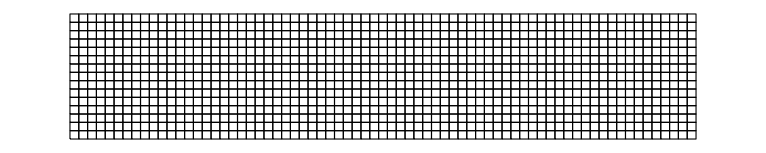

```mathematica
Unprotect[λ,μ,Subscript[ρ, 0],Subscript[ρ, 1],Subscript[ζ, 0],Subscript[ζ, 1],Ω^h,α, αΔT];
ClearAll[λ,μ,Subscript[ρ, 0],Subscript[ρ, 1],Subscript[ζ, 0],Subscript[ζ, 1],Ω^h,α, αΔT];
λ=1; μ=1; 
Subscript[ρ, 0]=0.5;Subscript[ρ, 1]=1.0;
Subscript[ζ, 0]=0.0;Subscript[ζ, 1]=0.1;
L̄=(Subscript[ζ, 1]-Subscript[ζ, 0])/π;
αΔT[ρ_,ζ_]=ρ;
Ω^h=ToElementMesh[Rectangle[{Subscript[ρ, 0],Subscript[ζ, 0]},{Subscript[ρ, 1],Subscript[ζ, 1]}],MaxCellMeasure->0.00005,"MeshElementType"->"QuadElement","MeshOrder"->2]
Protect[λ,μ,Subscript[ρ, 0],Subscript[ρ, 1],Subscript[ζ, 0],Subscript[ζ, 1],Ω^h,α,αΔT];
(Ω^h)["Wireframe"]
```

### Create Mesh and Mesh Data Structures

```mathematica
Unprotect[Subscript[n, np],Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, guass],Subscript[η, g],Subscript[n, eq],IEN,ID,ElementMesh,NMat];
ClearAll[Subscript[n, np],Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, guass],Subscript[η, g],Subscript[n, eq],IEN,ID,(*ElementMesh,*)NMat];
(x⃗)^h=(Ω^h)["Coordinates"];
Subscript[n, np]=Length@((x⃗)^h);
IEN=Apply[List,(Ω^h)["MeshElements"],{1}][[1,1]]ᵀ ;
NMat[ξ_,η_]={(N^(1))[ξ,η],(N^(2))[ξ,η],(N^(3))[ξ,η],(N^(4))[ξ,η],(N^(5))[ξ,η],(N^(6))[ξ,η],(N^(7))[ξ,η],(N^(8))[ξ,η]};
Subscript[n, en]=Dimensions[IEN][[1]];
Subscript[n, el]=Dimensions[IEN][[2]];
Subscript[n, dof]=3;
Subscript[n, guass]=9;
Subscript[η, g]=Subscript[SetUpη, g][(x⃗)^h] ;
ID=SetUpIDArray[];
Subscript[n, eq]=Max[ID];
(Ω^h)["PointElements"]={PointElement[Table[{i},{i,1,Subscript[n, np]}]]};
Protect[Subscript[n, np],Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, guass],Subscript[η, g],Subscript[n, eq],IEN,ID,ElementMesh, NMat];
```

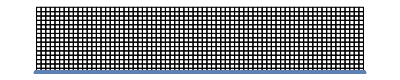

```mathematica
Show[
(Ω^h)["Wireframe"(*["MeshElement" -> "MeshElements","MeshElementIDStyle"->Blue]],
Ω^h["Wireframe"["MeshElement" -> "PointElements","MeshElementIDStyle"->Red]*)],
ListPlot[((x⃗)^h)[[Subscript[η, g][[1]]]],PlotMarkers->{Yellow,Large}],ListPlot[((x⃗)^h)[[Subscript[η, g][[2]]]],PlotMarkers->{Green}],ListPlot[((x⃗)^h)[[Subscript[η, g][[3]]]],PlotMarkers->{\[FreakedSmiley],Large}]]
```

```mathematica
ParallelEvaluate[$KernelID]
DistributeDefinitions[ComputeElementStiffnessMatrix,GuassIntegrate,ElementJacobian,CalculateGuassPoints,IEN,ID,λ,μ,k^e,f^e,NMat,ComputeElementStiffnessMatrixForStressProjection,ComputeGlobalForceMatrixForStressProjection,ComputeGlobalForceMatrixForStressProjection]
Clear[KMat,fMat];
ParallelEvaluate[KMat=SparseArray[{},{Subscript[n, eq],Subscript[n, eq]},0.0];];
ParallelEvaluate[fMat=SparseArray[{},{Subscript[n, eq]},0.0]];
ParallelMap[ComputeElementStiffnessMatrix,Range[Subscript[n, el]]]//AbsoluteTiming
{K1,K2,K3,K4,K5,K6,K7,K8}=ParallelEvaluate[KMat];
KMatP = K1+ K2 + K3+ K4 + K5+ K6 + K7+ K8;
ParallelMap[ComputeGlobalForceMatrix,Range[Subscript[n, el]]]//AbsoluteTiming
{f1,f2,f3,f4,f5,f6,f7,f8}=ParallelEvaluate[fMat];
fMatP = f1+ f2 + f3+ f4 + f5+ f6 + f7+ f8;
t1 = AbsoluteTime[];
sol1=LinearSolve[KMatP,fMatP];
t2 = AbsoluteTime[]-t1
UMat=SplitSolution[sol1];
{Subscript[Un, 1],Subscript[Un, 2],Subscript[Un, 3]}=Table[ElementMeshInterpolation[{Ω^h}, UMat[[i,;;]]//Normal],{i,1,Subscript[n, dof]}];
```

{1,2,3,4,5,6,7,8}

{ComputeElementStiffnessMatrix,ElementJacobian,W,μ,L̄,λ,αΔT,IEN,(x⃗)^h,N_(,ξ)^(1),N_(,ξ)^(2),N_(,ξ)^(3),N_(,ξ)^(4),N_(,ξ)^(5),N_(,ξ)^(6),N_(,ξ)^(7),N_(,ξ)^(8),N_(,η)^(1),N_(,η)^(2),N_(,η)^(3),N_(,η)^(4),N_(,η)^(5),N_(,η)^(6),N_(,η)^(7),N_(,η)^(8),n_en,NMat,n_dof,k^e,GuassIntegrate,CalculateGuassPoints,i,n_guass,Guass,N^(1),N^(2),N^(3),N^(4),N^(5),N^(6),N^(7),N^(8),ID,f^e,ComputeElementStiffnessMatrixForStressProjection,ComputeGlobalForceMatrixForStressProjection}

{174.454,{{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{8,8},{9,8},{10,8},{11,8},{12,8},{13,8},{14,8},{15,8},{16,8},{17,8},{18,8},{19,8},{20,8},{21,8},{22,8},{23,8},{24,8},{25,8},{26,8},{27,8},{28,7},{29,7},{30,7},{31,7},{32,7},{33,7},{34,7},{35,7},{36,7},{37,7},{38,7},{39,7},{40,7},{41,7},{42,7},{43,7},{44,7},{45,7},{46,7},{47,7},{48,7},{49,7},{50,7},{51,7},{52,7},{53,7},{54,7},{55,6},{56,6},{57,6},{58,6},{59,6},{60,6},{61,6},{62,6},{63,6},{64,6},{65,6},{66,6},{67,6},{68,6},{69,6},{70,6},{71,6},{72,6},{73,6},{74,6},{75,6},{76,6},{77,6},{78,6},{79,6},{80,6},{81,6},{82,5},{83,5},{84,5},{85,5},{86,5},{87,5},{88,5},{89,5},{90,5},{91,5},{92,5},{93,5},{94,5},{95,5},{96,5},{97,5},{98,5},{99,5},{100,5},{101,5},{102,5},{103,5},{104,5},{105,5},{106,5},{107,5},{108,5},{109,4},{110,4},{111,4},{112,4},{113,4},{114,4},{115,4},{116,4},{117,4},{118,4},{119,4},{120,4},{121,4},{122,4},{123,4},{124,4},{125,4},{126,4},{127,4},{128,4},{129,4},{130,4},{131,4},{132,4},{133,4},{134,4},{135,4},{136,3},{137,3},{138,3},{139,3},{140,3},{141,3},{142,3},{143,3},{144,3},{145,3},{146,3},{147,3},{148,3},{149,3},{150,3},{151,3},{152,3},{153,3},{154,3},{155,3},{156,3},{157,3},{158,3},{159,3},{160,3},{161,3},{162,3},{163,2},{164,2},{165,2},{166,2},{167,2},{168,2},{169,2},{170,2},{171,2},{172,2},{173,2},{174,2},{175,2},{176,2},{177,2},{178,2},{179,2},{180,2},{181,2},{182,2},{183,2},{184,2},{185,2},{186,2},{187,2},{188,2},{189,2},{190,1},{191,1},{192,1},{193,1},{194,1},{195,1},{196,1},{197,1},{198,1},{199,1},{200,1},{201,1},{202,1},{203,1},{204,1},{205,1},{206,1},{207,1},{208,1},{209,1},{210,1},{211,1},{212,1},{213,1},{214,1},{215,1},{216,1},{217,1},{218,1},{219,1},{220,1},{221,1},{222,1},{223,1},{224,1},{225,1},{226,1},{227,1},{228,1},{229,1},{230,1},{231,1},{232,1},{233,1},{234,1},{235,1},{236,1},{237,1},{238,1},{239,1},{240,1},{241,1},{242,1},{243,1},{244,7},{245,7},{246,7},{247,7},{248,7},{249,7},{250,7},{251,7},{252,7},{253,7},{254,7},{255,7},{256,7},{257,7},{258,7},{259,7},{260,7},{261,7},{262,7},{263,7},{264,7},{265,7},{266,7},{267,7},{268,7},{269,7},{270,7},{271,8},{272,8},{273,8},{274,8},{275,8},{276,8},{277,8},{278,8},{279,8},{280,8},{281,8},{282,8},{283,8},{284,8},{285,8},{286,8},{287,8},{288,8},{289,8},{290,8},{291,8},{292,8},{293,8},{294,8},{295,8},{296,8},{297,8},{298,2},{299,2},{300,2},{301,2},{302,2},{303,2},{304,2},{305,2},{306,2},{307,2},{308,2},{309,2},{310,2},{311,2},{312,2},{313,2},{314,2},{315,2},{316,2},{317,2},{318,2},{319,2},{320,2},{321,2},{322,2},{323,2},{324,2},{325,3},{326,3},{327,3},{328,3},{329,3},{330,3},{331,3},{332,3},{333,3},{334,3},{335,3},{336,3},{337,3},{338,3},{339,3},{340,3},{341,3},{342,3},{343,3},{344,3},{345,3},{346,3},{347,3},{348,3},{349,3},{350,3},{351,3},{352,6},{353,6},{354,6},{355,6},{356,6},{357,6},{358,6},{359,6},{360,6},{361,6},{362,6},{363,6},{364,6},{365,6},{366,6},{367,6},{368,6},{369,6},{370,6},{371,6},{372,6},{373,6},{374,6},{375,6},{376,6},{377,6},{378,6},{379,4},{380,4},{381,4},{382,4},{383,4},{384,4},{385,4},{386,4},{387,4},{388,4},{389,4},{390,4},{391,4},{392,4},{393,4},{394,4},{395,4},{396,4},{397,4},{398,4},{399,4},{400,4},{401,4},{402,4},{403,4},{404,4},{405,4},{406,5},{407,5},{408,5},{409,5},{410,5},{411,5},{412,5},{413,5},{414,5},{415,5},{416,5},{417,5},{418,5},{419,5},{420,5},{421,5},{422,5},{423,5},{424,5},{425,5},{426,5},{427,5},{428,5},{429,5},{430,5},{431,5},{432,5},{433,1},{434,1},{435,1},{436,1},{437,1},{438,1},{439,1},{440,1},{441,1},{442,1},{443,1},{444,1},{445,1},{446,1},{447,1},{448,1},{449,1},{450,1},{451,1},{452,1},{453,1},{454,1},{455,1},{456,1},{457,1},{458,1},{459,1},{460,8},{461,8},{462,8},{463,8},{464,8},{465,8},{466,8},{467,8},{468,8},{469,8},{470,8},{471,8},{472,8},{473,8},{474,8},{475,8},{476,8},{477,8},{478,8},{479,8},{480,8},{481,8},{482,8},{483,8},{484,8},{485,8},{486,8},{487,2},{488,2},{489,2},{490,2},{491,2},{492,2},{493,2},{494,2},{495,2},{496,2},{497,2},{498,2},{499,2},{500,2},{501,2},{502,2},{503,2},{504,2},{505,2},{506,2},{507,2},{508,2},{509,2},{510,2},{511,2},{512,2},{513,2},{514,6},{515,6},{516,6},{517,6},{518,6},{519,6},{520,6},{521,6},{522,6},{523,6},{524,6},{525,6},{526,6},{527,6},{528,6},{529,6},{530,6},{531,6},{532,6},{533,6},{534,6},{535,6},{536,6},{537,6},{538,6},{539,6},{540,6},{541,7},{542,7},{543,7},{544,7},{545,7},{546,7},{547,7},{548,7},{549,7},{550,7},{551,7},{552,7},{553,7},{554,7},{555,7},{556,7},{557,7},{558,7},{559,7},{560,7},{561,7},{562,7},{563,7},{564,7},{565,7},{566,7},{567,7},{568,4},{569,4},{570,4},{571,4},{572,4},{573,4},{574,4},{575,4},{576,4},{577,4},{578,4},{579,4},{580,4},{581,4},{582,4},{583,4},{584,4},{585,4},{586,4},{587,4},{588,4},{589,4},{590,4},{591,4},{592,4},{593,4},{594,4},{595,3},{596,3},{597,3},{598,3},{599,3},{600,3},{601,3},{602,3},{603,3},{604,3},{605,3},{606,3},{607,3},{608,3},{609,3},{610,3},{611,3},{612,3},{613,3},{614,3},{615,3},{616,3},{617,3},{618,3},{619,3},{620,3},{621,3},{622,2},{623,2},{624,2},{625,2},{626,2},{627,2},{628,2},{629,2},{630,2},{631,2},{632,2},{633,2},{634,2},{635,2},{636,2},{637,2},{638,2},{639,2},{640,2},{641,2},{642,2},{643,2},{644,2},{645,2},{646,2},{647,2},{648,2},{649,5},{650,5},{651,5},{652,5},{653,5},{654,5},{655,5},{656,5},{657,5},{658,5},{659,5},{660,5},{661,5},{662,5},{663,5},{664,5},{665,5},{666,5},{667,5},{668,5},{669,5},{670,5},{671,5},{672,5},{673,5},{674,5},{675,5},{676,1},{677,1},{678,1},{679,1},{680,1},{681,1},{682,1},{683,1},{684,1},{685,1},{686,1},{687,1},{688,1},{689,1},{690,1},{691,1},{692,1},{693,1},{694,1},{695,1},{696,1},{697,1},{698,1},{699,1},{700,1},{701,1},{702,6},{703,6},{704,6},{705,6},{706,6},{707,6},{708,6},{709,6},{710,6},{711,6},{712,6},{713,6},{714,6},{715,6},{716,6},{717,6},{718,6},{719,6},{720,6},{721,6},{722,6},{723,6},{724,6},{725,6},{726,6},{727,6},{728,8},{729,8},{730,8},{731,8},{732,8},{733,8},{734,8},{735,8},{736,8},{737,8},{738,8},{739,8},{740,8},{741,8},{742,8},{743,8},{744,8},{745,8},{746,8},{747,8},{748,8},{749,8},{750,8},{751,8},{752,8},{753,8},{754,4},{755,4},{756,4},{757,4},{758,4},{759,4},{760,4},{761,4},{762,4},{763,4},{764,4},{765,4},{766,4},{767,4},{768,4},{769,4},{770,4},{771,4},{772,4},{773,4},{774,4},{775,4},{776,4},{777,4},{778,4},{779,4},{780,3},{781,3},{782,3},{783,3},{784,3},{785,3},{786,3},{787,3},{788,3},{789,3},{790,3},{791,3},{792,3},{793,3},{794,3},{795,3},{796,3},{797,3},{798,3},{799,3},{800,3},{801,3},{802,3},{803,3},{804,3},{805,3},{806,1},{807,1},{808,1},{809,1},{810,1},{811,1},{812,1},{813,1},{814,1},{815,1},{816,1},{817,1},{818,1},{819,1},{820,1},{821,1},{822,1},{823,1},{824,1},{825,1},{826,1},{827,1},{828,1},{829,1},{830,1},{831,1},{832,2},{833,2},{834,2},{835,2},{836,2},{837,2},{838,2},{839,2},{840,2},{841,2},{842,2},{843,2},{844,2},{845,2},{846,2},{847,2},{848,2},{849,2},{850,2},{851,2},{852,2},{853,2},{854,2},{855,2},{856,2},{857,2},{858,5},{859,5},{860,5},{861,5},{862,5},{863,5},{864,5},{865,5},{866,5},{867,5},{868,5},{869,5},{870,5},{871,5},{872,5},{873,5},{874,5},{875,5},{876,5},{877,5},{878,5},{879,5},{880,5},{881,5},{882,5},{883,5},{884,7},{885,7},{886,7},{887,7},{888,7},{889,7},{890,7},{891,7},{892,7},{893,7},{894,7},{895,7},{896,7},{897,7},{898,7},{899,7},{900,7},{901,7},{902,7},{903,7},{904,7},{905,7},{906,7},{907,7},{908,7},{909,7},{910,6},{911,6},{912,6},{913,6},{914,6},{915,6},{916,6},{917,6},{918,6},{919,6},{920,6},{921,6},{922,6},{923,6},{924,6},{925,6},{926,6},{927,6},{928,6},{929,6},{930,6},{931,6},{932,6},{933,6},{934,6},{935,6},{936,8},{937,8},{938,8},{939,8},{940,8},{941,8},{942,8},{943,8},{944,8},{945,8},{946,8},{947,8},{948,8},{949,8},{950,8},{951,8},{952,8},{953,8},{954,8},{955,8},{956,8},{957,8},{958,8},{959,8},{960,8},{961,8},{962,3},{963,3},{964,3},{965,3},{966,3},{967,3},{968,3},{969,3},{970,3},{971,3},{972,3},{973,3},{974,3},{975,3},{976,3},{977,3},{978,3},{979,3},{980,3},{981,3},{982,3},{983,3},{984,3},{985,3},{986,3},{987,3},{988,1},{989,1},{990,1},{991,1},{992,1},{993,1},{994,1},{995,1},{996,1},{997,1},{998,1},{999,1},{1000,1},{1001,1},{1002,1},{1003,1},{1004,1},{1005,1},{1006,1},{1007,1},{1008,1},{1009,1},{1010,1},{1011,1},{1012,1},{1013,1},{1014,4},{1015,4},{1016,4},{1017,4},{1018,4},{1019,4},{1020,4},{1021,4},{1022,4},{1023,4},{1024,4},{1025,4},{1026,4},{1027,4},{1028,4},{1029,4},{1030,4},{1031,4},{1032,4},{1033,4},{1034,4},{1035,4},{1036,4},{1037,4},{1038,4},{1039,4},{1040,5},{1041,5},{1042,5},{1043,5},{1044,5},{1045,5},{1046,5},{1047,5},{1048,5},{1049,5},{1050,5},{1051,5},{1052,5},{1053,5},{1054,5},{1055,5},{1056,5},{1057,5},{1058,5},{1059,5},{1060,5},{1061,5},{1062,5},{1063,5},{1064,5},{1065,5}}}

{8.30488,{{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{8,8},{9,8},{10,8},{11,8},{12,8},{13,8},{14,8},{15,8},{16,8},{17,8},{18,8},{19,8},{20,8},{21,8},{22,8},{23,8},{24,8},{25,8},{26,8},{27,8},{28,7},{29,7},{30,7},{31,7},{32,7},{33,7},{34,7},{35,7},{36,7},{37,7},{38,7},{39,7},{40,7},{41,7},{42,7},{43,7},{44,7},{45,7},{46,7},{47,7},{48,7},{49,7},{50,7},{51,7},{52,7},{53,7},{54,7},{55,6},{56,6},{57,6},{58,6},{59,6},{60,6},{61,6},{62,6},{63,6},{64,6},{65,6},{66,6},{67,6},{68,6},{69,6},{70,6},{71,6},{72,6},{73,6},{74,6},{75,6},{76,6},{77,6},{78,6},{79,6},{80,6},{81,6},{82,5},{83,5},{84,5},{85,5},{86,5},{87,5},{88,5},{89,5},{90,5},{91,5},{92,5},{93,5},{94,5},{95,5},{96,5},{97,5},{98,5},{99,5},{100,5},{101,5},{102,5},{103,5},{104,5},{105,5},{106,5},{107,5},{108,5},{109,4},{110,4},{111,4},{112,4},{113,4},{114,4},{115,4},{116,4},{117,4},{118,4},{119,4},{120,4},{121,4},{122,4},{123,4},{124,4},{125,4},{126,4},{127,4},{128,4},{129,4},{130,4},{131,4},{132,4},{133,4},{134,4},{135,4},{136,3},{137,3},{138,3},{139,3},{140,3},{141,3},{142,3},{143,3},{144,3},{145,3},{146,3},{147,3},{148,3},{149,3},{150,3},{151,3},{152,3},{153,3},{154,3},{155,3},{156,3},{157,3},{158,3},{159,3},{160,3},{161,3},{162,3},{163,2},{164,2},{165,2},{166,2},{167,2},{168,2},{169,2},{170,2},{171,2},{172,2},{173,2},{174,2},{175,2},{176,2},{177,2},{178,2},{179,2},{180,2},{181,2},{182,2},{183,2},{184,2},{185,2},{186,2},{187,2},{188,2},{189,2},{190,1},{191,1},{192,1},{193,1},{194,1},{195,1},{196,1},{197,1},{198,1},{199,1},{200,1},{201,1},{202,1},{203,1},{204,1},{205,1},{206,1},{207,1},{208,1},{209,1},{210,1},{211,1},{212,1},{213,1},{214,1},{215,1},{216,1},{217,4},{218,4},{219,4},{220,4},{221,4},{222,4},{223,4},{224,4},{225,4},{226,4},{227,4},{228,4},{229,4},{230,4},{231,4},{232,4},{233,4},{234,4},{235,4},{236,4},{237,4},{238,4},{239,4},{240,4},{241,4},{242,4},{243,4},{244,3},{245,3},{246,3},{247,3},{248,3},{249,3},{250,3},{251,3},{252,3},{253,3},{254,3},{255,3},{256,3},{257,3},{258,3},{259,3},{260,3},{261,3},{262,3},{263,3},{264,3},{265,3},{266,3},{267,3},{268,3},{269,3},{270,3},{271,6},{272,6},{273,6},{274,6},{275,6},{276,6},{277,6},{278,6},{279,6},{280,6},{281,6},{282,6},{283,6},{284,6},{285,6},{286,6},{287,6},{288,6},{289,6},{290,6},{291,6},{292,6},{293,6},{294,6},{295,6},{296,6},{297,6},{298,1},{299,1},{300,1},{301,1},{302,1},{303,1},{304,1},{305,1},{306,1},{307,1},{308,1},{309,1},{310,1},{311,1},{312,1},{313,1},{314,1},{315,1},{316,1},{317,1},{318,1},{319,1},{320,1},{321,1},{322,1},{323,1},{324,1},{325,8},{326,8},{327,8},{328,8},{329,8},{330,8},{331,8},{332,8},{333,8},{334,8},{335,8},{336,8},{337,8},{338,8},{339,8},{340,8},{341,8},{342,8},{343,8},{344,8},{345,8},{346,8},{347,8},{348,8},{349,8},{350,8},{351,8},{352,7},{353,7},{354,7},{355,7},{356,7},{357,7},{358,7},{359,7},{360,7},{361,7},{362,7},{363,7},{364,7},{365,7},{366,7},{367,7},{368,7},{369,7},{370,7},{371,7},{372,7},{373,7},{374,7},{375,7},{376,7},{377,7},{378,7},{379,6},{380,6},{381,6},{382,6},{383,6},{384,6},{385,6},{386,6},{387,6},{388,6},{389,6},{390,6},{391,6},{392,6},{393,6},{394,6},{395,6},{396,6},{397,6},{398,6},{399,6},{400,6},{401,6},{402,6},{403,6},{404,6},{405,6},{406,4},{407,4},{408,4},{409,4},{410,4},{411,4},{412,4},{413,4},{414,4},{415,4},{416,4},{417,4},{418,4},{419,4},{420,4},{421,4},{422,4},{423,4},{424,4},{425,4},{426,4},{427,4},{428,4},{429,4},{430,4},{431,4},{432,4},{433,1},{434,1},{435,1},{436,1},{437,1},{438,1},{439,1},{440,1},{441,1},{442,1},{443,1},{444,1},{445,1},{446,1},{447,1},{448,1},{449,1},{450,1},{451,1},{452,1},{453,1},{454,1},{455,1},{456,1},{457,1},{458,1},{459,1},{460,2},{461,2},{462,2},{463,2},{464,2},{465,2},{466,2},{467,2},{468,2},{469,2},{470,2},{471,2},{472,2},{473,2},{474,2},{475,2},{476,2},{477,2},{478,2},{479,2},{480,2},{481,2},{482,2},{483,2},{484,2},{485,2},{486,2},{487,8},{488,8},{489,8},{490,8},{491,8},{492,8},{493,8},{494,8},{495,8},{496,8},{497,8},{498,8},{499,8},{500,8},{501,8},{502,8},{503,8},{504,8},{505,8},{506,8},{507,8},{508,8},{509,8},{510,8},{511,8},{512,8},{513,8},{514,7},{515,7},{516,7},{517,7},{518,7},{519,7},{520,7},{521,7},{522,7},{523,7},{524,7},{525,7},{526,7},{527,7},{528,7},{529,7},{530,7},{531,7},{532,7},{533,7},{534,7},{535,7},{536,7},{537,7},{538,7},{539,7},{540,7},{541,6},{542,6},{543,6},{544,6},{545,6},{546,6},{547,6},{548,6},{549,6},{550,6},{551,6},{552,6},{553,6},{554,6},{555,6},{556,6},{557,6},{558,6},{559,6},{560,6},{561,6},{562,6},{563,6},{564,6},{565,6},{566,6},{567,6},{568,4},{569,4},{570,4},{571,4},{572,4},{573,4},{574,4},{575,4},{576,4},{577,4},{578,4},{579,4},{580,4},{581,4},{582,4},{583,4},{584,4},{585,4},{586,4},{587,4},{588,4},{589,4},{590,4},{591,4},{592,4},{593,4},{594,4},{595,1},{596,1},{597,1},{598,1},{599,1},{600,1},{601,1},{602,1},{603,1},{604,1},{605,1},{606,1},{607,1},{608,1},{609,1},{610,1},{611,1},{612,1},{613,1},{614,1},{615,1},{616,1},{617,1},{618,1},{619,1},{620,1},{621,1},{622,8},{623,8},{624,8},{625,8},{626,8},{627,8},{628,8},{629,8},{630,8},{631,8},{632,8},{633,8},{634,8},{635,8},{636,8},{637,8},{638,8},{639,8},{640,8},{641,8},{642,8},{643,8},{644,8},{645,8},{646,8},{647,8},{648,8},{649,5},{650,5},{651,5},{652,5},{653,5},{654,5},{655,5},{656,5},{657,5},{658,5},{659,5},{660,5},{661,5},{662,5},{663,5},{664,5},{665,5},{666,5},{667,5},{668,5},{669,5},{670,5},{671,5},{672,5},{673,5},{674,5},{675,5},{676,7},{677,7},{678,7},{679,7},{680,7},{681,7},{682,7},{683,7},{684,7},{685,7},{686,7},{687,7},{688,7},{689,7},{690,7},{691,7},{692,7},{693,7},{694,7},{695,7},{696,7},{697,7},{698,7},{699,7},{700,7},{701,7},{702,6},{703,6},{704,6},{705,6},{706,6},{707,6},{708,6},{709,6},{710,6},{711,6},{712,6},{713,6},{714,6},{715,6},{716,6},{717,6},{718,6},{719,6},{720,6},{721,6},{722,6},{723,6},{724,6},{725,6},{726,6},{727,6},{728,1},{729,1},{730,1},{731,1},{732,1},{733,1},{734,1},{735,1},{736,1},{737,1},{738,1},{739,1},{740,1},{741,1},{742,1},{743,1},{744,1},{745,1},{746,1},{747,1},{748,1},{749,1},{750,1},{751,1},{752,1},{753,1},{754,7},{755,7},{756,7},{757,7},{758,7},{759,7},{760,7},{761,7},{762,7},{763,7},{764,7},{765,7},{766,7},{767,7},{768,7},{769,7},{770,7},{771,7},{772,7},{773,7},{774,7},{775,7},{776,7},{777,7},{778,7},{779,7},{780,6},{781,6},{782,6},{783,6},{784,6},{785,6},{786,6},{787,6},{788,6},{789,6},{790,6},{791,6},{792,6},{793,6},{794,6},{795,6},{796,6},{797,6},{798,6},{799,6},{800,6},{801,6},{802,6},{803,6},{804,6},{805,6},{806,5},{807,5},{808,5},{809,5},{810,5},{811,5},{812,5},{813,5},{814,5},{815,5},{816,5},{817,5},{818,5},{819,5},{820,5},{821,5},{822,5},{823,5},{824,5},{825,5},{826,5},{827,5},{828,5},{829,5},{830,5},{831,5},{832,8},{833,8},{834,8},{835,8},{836,8},{837,8},{838,8},{839,8},{840,8},{841,8},{842,8},{843,8},{844,8},{845,8},{846,8},{847,8},{848,8},{849,8},{850,8},{851,8},{852,8},{853,8},{854,8},{855,8},{856,8},{857,8},{858,1},{859,1},{860,1},{861,1},{862,1},{863,1},{864,1},{865,1},{866,1},{867,1},{868,1},{869,1},{870,1},{871,1},{872,1},{873,1},{874,1},{875,1},{876,1},{877,1},{878,1},{879,1},{880,1},{881,1},{882,1},{883,1},{884,7},{885,7},{886,7},{887,7},{888,7},{889,7},{890,7},{891,7},{892,7},{893,7},{894,7},{895,7},{896,7},{897,7},{898,7},{899,7},{900,7},{901,7},{902,7},{903,7},{904,7},{905,7},{906,7},{907,7},{908,7},{909,7},{910,6},{911,6},{912,6},{913,6},{914,6},{915,6},{916,6},{917,6},{918,6},{919,6},{920,6},{921,6},{922,6},{923,6},{924,6},{925,6},{926,6},{927,6},{928,6},{929,6},{930,6},{931,6},{932,6},{933,6},{934,6},{935,6},{936,3},{937,3},{938,3},{939,3},{940,3},{941,3},{942,3},{943,3},{944,3},{945,3},{946,3},{947,3},{948,3},{949,3},{950,3},{951,3},{952,3},{953,3},{954,3},{955,3},{956,3},{957,3},{958,3},{959,3},{960,3},{961,3},{962,2},{963,2},{964,2},{965,2},{966,2},{967,2},{968,2},{969,2},{970,2},{971,2},{972,2},{973,2},{974,2},{975,2},{976,2},{977,2},{978,2},{979,2},{980,2},{981,2},{982,2},{983,2},{984,2},{985,2},{986,2},{987,2},{988,4},{989,4},{990,4},{991,4},{992,4},{993,4},{994,4},{995,4},{996,4},{997,4},{998,4},{999,4},{1000,4},{1001,4},{1002,4},{1003,4},{1004,4},{1005,4},{1006,4},{1007,4},{1008,4},{1009,4},{1010,4},{1011,4},{1012,4},{1013,4},{1014,1},{1015,1},{1016,1},{1017,1},{1018,1},{1019,1},{1020,1},{1021,1},{1022,1},{1023,1},{1024,1},{1025,1},{1026,1},{1027,1},{1028,1},{1029,1},{1030,1},{1031,1},{1032,1},{1033,1},{1034,1},{1035,1},{1036,1},{1037,1},{1038,1},{1039,1},{1040,5},{1041,5},{1042,5},{1043,5},{1044,5},{1045,5},{1046,5},{1047,5},{1048,5},{1049,5},{1050,5},{1051,5},{1052,5},{1053,5},{1054,5},{1055,5},{1056,5},{1057,5},{1058,5},{1059,5},{1060,5},{1061,5},{1062,5},{1063,5},{1064,5},{1065,5}}}

0.143752

### Post Processing

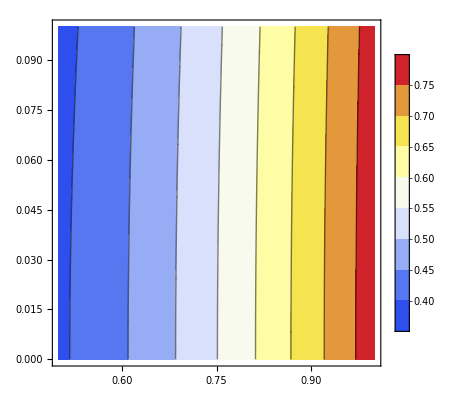

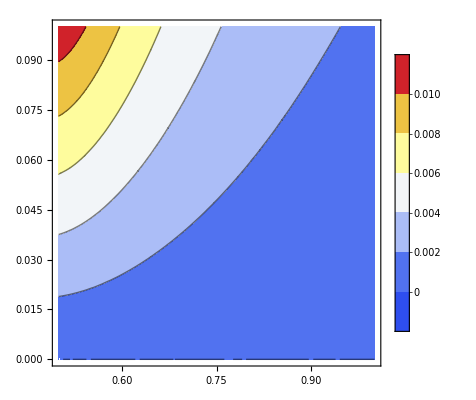

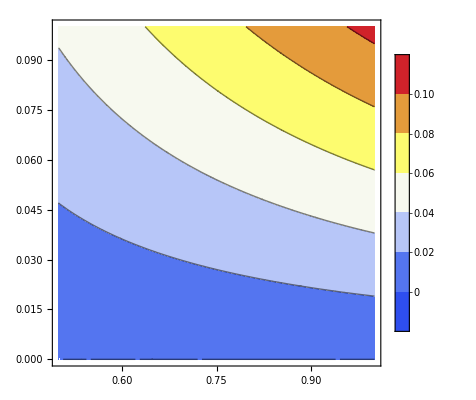

```mathematica
ContourPlot[Subscript[Un, 1][ρ,ζ],{ρ,ζ}∈Ω^h,ColorFunction->"Temperature",AspectRatio->1,PlotLegends->Automatic,PlotRange->All]
ContourPlot[Subscript[Un, 2][ρ,ζ],{ρ,ζ}∈Ω^h,ColorFunction->"Temperature",AspectRatio->1,PlotLegends->Automatic,PlotRange->All]
ContourPlot[Subscript[Un, 3][ρ,ζ],{ρ,ζ}∈Ω^h,ColorFunction->"Temperature",AspectRatio->1,PlotLegends->Automatic,PlotRange->All]
```

### Verify boundary conditions

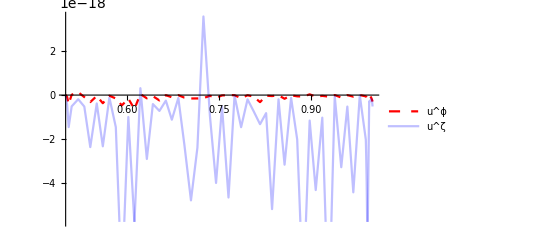

```mathematica
Plot[{Subscript[Un, 2][ρ,Subscript[ζ, 0]],Subscript[Un, 3][ρ,Subscript[ζ, 0]]},{ρ,Subscript[ρ, 0],Subscript[ρ, 1]},PlotStyle->{{Red,Dashed},{Blue,Opacity[0.25]}},PlotLegends->{"u^ϕ","u^ζ"}]
```

### Computing derivatives for u^ρ, u^ϕ , u^ζ w.r.t {ρ, ζ}

```mathematica
ClearAll[aMat,l11Mat,l13Mat,l21Mat,l23Mat,l31Mat,l33Mat];
ParallelEvaluate[aMat=SparseArray[{},{Subscript[n, np],Subscript[n, np]},0.0];];
ParallelEvaluate[l11Mat=l13Mat=l21Mat=l23Mat=l31Mat=l33Mat= SparseArray[{},{Subscript[n, np]},0.0]];
ParallelMap[ComputeElementStiffnessMatrixForStressProjection,Range[Subscript[n, el]]]//AbsoluteTiming
{aP1,aP2,aP3,aP4,aP5,aP6,aP7,aP8}=ParallelEvaluate[aMat];
```

{17.6241,{{Removed[e$205616],8},{Removed[e$205746],8},{Removed[e$205876],8},{Removed[e$206027],8},{Removed[e$206176],8},{Removed[e$206306],8},{Removed[e$206566],8},{Removed[e$206715],8},{Removed[e$206897],8},{Removed[e$207027],8},{Removed[e$207157],8},{Removed[e$207287],8},{Removed[e$207642],8},{Removed[e$208009],8},{Removed[e$208163],8},{Removed[e$208293],8},{Removed[e$208423],8},{Removed[e$208553],8},{Removed[e$208704],8},{Removed[e$208853],8},{Removed[e$208983],8},{Removed[e$209208],8},{Removed[e$209348],8},{Removed[e$209521],8},{Removed[e$209652],8},{Removed[e$209782],8},{Removed[e$209912],8},{Removed[e$159031],7},{Removed[e$159173],7},{Removed[e$159304],7},{Removed[e$159434],7},{Removed[e$159575],7},{Removed[e$159705],7},{Removed[e$159934],7},{Removed[e$160083],7},{Removed[e$160214],7},{Removed[e$160425],7},{Removed[e$160574],7},{Removed[e$160705],7},{Removed[e$160835],7},{Removed[e$160965],7},{Removed[e$161095],7},{Removed[e$161490],7},{Removed[e$161649],7},{Removed[e$161780],7},{Removed[e$161910],7},{Removed[e$162051],7},{Removed[e$162181],7},{Removed[e$162450],7},{Removed[e$162599],7},{Removed[e$162729],7},{Removed[e$163005],7},{Removed[e$163225],7},{Removed[e$163356],7},{Removed[e$171685],6},{Removed[e$171815],6},{Removed[e$171945],6},{Removed[e$172075],6},{Removed[e$172205],6},{Removed[e$172335],6},{Removed[e$172465],6},{Removed[e$172614],6},{Removed[e$172744],6},{Removed[e$172920],6},{Removed[e$173060],6},{Removed[e$173190],6},{Removed[e$173364],6},{Removed[e$173549],6},{Removed[e$173679],6},{Removed[e$173809],6},{Removed[e$173939],6},{Removed[e$174069],6},{Removed[e$174199],6},{Removed[e$174329],6},{Removed[e$174459],6},{Removed[e$174589],6},{Removed[e$174729],6},{Removed[e$174859],6},{Removed[e$174991],6},{Removed[e$175121],6},{Removed[e$175251],6},{Removed[e$199664],5},{Removed[e$199925],5},{Removed[e$200055],5},{Removed[e$200211],5},{Removed[e$200341],5},{Removed[e$200471],5},{Removed[e$200817],5},{Removed[e$201006],5},{Removed[e$201136],5},{Removed[e$201266],5},{Removed[e$201764],5},{Removed[e$201909],5},{Removed[e$202770],5},{Removed[e$203253],5},{Removed[e$203526],5},{Removed[e$204936],5},{Removed[e$205364],5},{Removed[e$205763],5},{Removed[e$206131],5},{Removed[e$206294],5},{Removed[e$206437],5},{Removed[e$207512],5},{Removed[e$208512],5},{Removed[e$208887],5},{Removed[e$209021],5},{Removed[e$209295],5},{Removed[e$209425],5},{Removed[e$189828],4},{Removed[e$189958],4},{Removed[e$190088],4},{Removed[e$190218],4},{Removed[e$190348],4},{Removed[e$190479],4},{Removed[e$190609],4},{Removed[e$190740],4},{Removed[e$190871],4},{Removed[e$191073],4},{Removed[e$191230],4},{Removed[e$191365],4},{Removed[e$191496],4},{Removed[e$191669],4},{Removed[e$191799],4},{Removed[e$192047],4},{Removed[e$192196],4},{Removed[e$192326],4},{Removed[e$192477],4},{Removed[e$192607],4},{Removed[e$192742],4},{Removed[e$192872],4},{Removed[e$193003],4},{Removed[e$193134],4},{Removed[e$193319],4},{Removed[e$193488],4},{Removed[e$193623],4},{Removed[e$181133],3},{Removed[e$181263],3},{Removed[e$181393],3},{Removed[e$181523],3},{Removed[e$181653],3},{Removed[e$181783],3},{Removed[e$181951],3},{Removed[e$182081],3},{Removed[e$182223],3},{Removed[e$182353],3},{Removed[e$182484],3},{Removed[e$182616],3},{Removed[e$182837],3},{Removed[e$183094],3},{Removed[e$183240],3},{Removed[e$183371],3},{Removed[e$183501],3},{Removed[e$183631],3},{Removed[e$183761],3},{Removed[e$183891],3},{Removed[e$184021],3},{Removed[e$184189],3},{Removed[e$184319],3},{Removed[e$184476],3},{Removed[e$184606],3},{Removed[e$184737],3},{Removed[e$184868],3},{Removed[e$186844],2},{Removed[e$186974],2},{Removed[e$187104],2},{Removed[e$187234],2},{Removed[e$187364],2},{Removed[e$187494],2},{Removed[e$187688],2},{Removed[e$187818],2},{Removed[e$187948],2},{Removed[e$188183],2},{Removed[e$188405],2},{Removed[e$188535],2},{Removed[e$188665],2},{Removed[e$188795],2},{Removed[e$188925],2},{Removed[e$189134],2},{Removed[e$189264],2},{Removed[e$189394],2},{Removed[e$189524],2},{Removed[e$189654],2},{Removed[e$189784],2},{Removed[e$189978],2},{Removed[e$190127],2},{Removed[e$190257],2},{Removed[e$190475],2},{Removed[e$190688],2},{Removed[e$190818],2},{Removed[e$195614],1},{Removed[e$195744],1},{Removed[e$195874],1},{Removed[e$196004],1},{Removed[e$196134],1},{Removed[e$196264],1},{Removed[e$196394],1},{Removed[e$196524],1},{Removed[e$196654],1},{Removed[e$196784],1},{Removed[e$196914],1},{Removed[e$197044],1},{Removed[e$197174],1},{Removed[e$197304],1},{Removed[e$197434],1},{Removed[e$197564],1},{Removed[e$197694],1},{Removed[e$197824],1},{Removed[e$197954],1},{Removed[e$198084],1},{Removed[e$198214],1},{Removed[e$198344],1},{Removed[e$198474],1},{Removed[e$198604],1},{Removed[e$198734],1},{Removed[e$198864],1},{Removed[e$198994],1},{Removed[e$210192],8},{Removed[e$210324],8},{Removed[e$210473],8},{Removed[e$210603],8},{Removed[e$210733],8},{Removed[e$210863],8},{Removed[e$211032],8},{Removed[e$211331],8},{Removed[e$211476],8},{Removed[e$211606],8},{Removed[e$211736],8},{Removed[e$211866],8},{Removed[e$211996],8},{Removed[e$212145],8},{Removed[e$212275],8},{Removed[e$212488],8},{Removed[e$212620],8},{Removed[e$212793],8},{Removed[e$212923],8},{Removed[e$213053],8},{Removed[e$213183],8},{Removed[e$213407],8},{Removed[e$213668],8},{Removed[e$213822],8},{Removed[e$213952],8},{Removed[e$214082],8},{Removed[e$214212],8},{Removed[e$163487],7},{Removed[e$163617],7},{Removed[e$163747],7},{Removed[e$163924],7},{Removed[e$164064],7},{Removed[e$164195],7},{Removed[e$164325],7},{Removed[e$164455],7},{Removed[e$164585],7},{Removed[e$164980],7},{Removed[e$165149],7},{Removed[e$165280],7},{Removed[e$165410],7},{Removed[e$165912],7},{Removed[e$166090],7},{Removed[e$167229],7},{Removed[e$168444],7},{Removed[e$168797],7},{Removed[e$170294],7},{Removed[e$170863],7},{Removed[e$171356],7},{Removed[e$171811],7},{Removed[e$172212],7},{Removed[e$172427],7},{Removed[e$173819],7},{Removed[e$175078],7},{Removed[e$175516],7},{Removed[e$193754],4},{Removed[e$193927],4},{Removed[e$194057],4},{Removed[e$194280],4},{Removed[e$194429],4},{Removed[e$194559],4},{Removed[e$194710],4},{Removed[e$194840],4},{Removed[e$194975],4},{Removed[e$195105],4},{Removed[e$195236],4},{Removed[e$195367],4},{Removed[e$195543],4},{Removed[e$195693],4},{Removed[e$195828],4},{Removed[e$195959],4},{Removed[e$196127],4},{Removed[e$196257],4},{Removed[e$196507],4},{Removed[e$196656],4},{Removed[e$196786],4},{Removed[e$196937],4},{Removed[e$197067],4},{Removed[e$197203],4},{Removed[e$197333],4},{Removed[e$197464],4},{Removed[e$197595],4},{Removed[e$199124],1},{Removed[e$199254],1},{Removed[e$199384],1},{Removed[e$199514],1},{Removed[e$199644],1},{Removed[e$199774],1},{Removed[e$199904],1},{Removed[e$200034],1},{Removed[e$200164],1},{Removed[e$200294],1},{Removed[e$200424],1},{Removed[e$200554],1},{Removed[e$200684],1},{Removed[e$200814],1},{Removed[e$200944],1},{Removed[e$201074],1},{Removed[e$201204],1},{Removed[e$201334],1},{Removed[e$201464],1},{Removed[e$201594],1},{Removed[e$201724],1},{Removed[e$201854],1},{Removed[e$201984],1},{Removed[e$202114],1},{Removed[e$202244],1},{Removed[e$202374],1},{Removed[e$202504],1},{Removed[e$190948],2},{Removed[e$191078],2},{Removed[e$191208],2},{Removed[e$191432],2},{Removed[e$191562],2},{Removed[e$191692],2},{Removed[e$191822],2},{Removed[e$191952],2},{Removed[e$192082],2},{Removed[e$192275],2},{Removed[e$192405],2},{Removed[e$192535],2},{Removed[e$192777],2},{Removed[e$192972],2},{Removed[e$193102],2},{Removed[e$193232],2},{Removed[e$193362],2},{Removed[e$193492],2},{Removed[e$193722],2},{Removed[e$193852],2},{Removed[e$193982],2},{Removed[e$194112],2},{Removed[e$194242],2},{Removed[e$194372],2},{Removed[e$194566],2},{Removed[e$194696],2},{Removed[e$194826],2},{Removed[e$175383],6},{Removed[e$175513],6},{Removed[e$175643],6},{Removed[e$175773],6},{Removed[e$175903],6},{Removed[e$176033],6},{Removed[e$176163],6},{Removed[e$176293],6},{Removed[e$176423],6},{Removed[e$176553],6},{Removed[e$176693],6},{Removed[e$176823],6},{Removed[e$176955],6},{Removed[e$177085],6},{Removed[e$177215],6},{Removed[e$177347],6},{Removed[e$177477],6},{Removed[e$177607],6},{Removed[e$177737],6},{Removed[e$177867],6},{Removed[e$177997],6},{Removed[e$178127],6},{Removed[e$178257],6},{Removed[e$178387],6},{Removed[e$178517],6},{Removed[e$178648],6},{Removed[e$178778],6},{Removed[e$209791],5},{Removed[e$210118],5},{Removed[e$210267],5},{Removed[e$210637],5},{Removed[e$210931],5},{Removed[e$211061],5},{Removed[e$211217],5},{Removed[e$211347],5},{Removed[e$211477],5},{Removed[e$211939],5},{Removed[e$212187],5},{Removed[e$212317],5},{Removed[e$212447],5},{Removed[e$212721],5},{Removed[e$212851],5},{Removed[e$213217],5},{Removed[e$213544],5},{Removed[e$213714],5},{Removed[e$214084],5},{Removed[e$214378],5},{Removed[e$214508],5},{Removed[e$214664],5},{Removed[e$214794],5},{Removed[e$214924],5},{Removed[e$215363],5},{Removed[e$215611],5},{Removed[e$215741],5},{Removed[e$214342],8},{Removed[e$214472],8},{Removed[e$214602],8},{Removed[e$214732],8},{Removed[e$214881],8},{Removed[e$215011],8},{Removed[e$215223],8},{Removed[e$215355],8},{Removed[e$215528],8},{Removed[e$215658],8},{Removed[e$215788],8},{Removed[e$215918],8},{Removed[e$216187],8},{Removed[e$216448],8},{Removed[e$216602],8},{Removed[e$216732],8},{Removed[e$216862],8},{Removed[e$216992],8},{Removed[e$217122],8},{Removed[e$217271],8},{Removed[e$217401],8},{Removed[e$217606],8},{Removed[e$217738],8},{Removed[e$217911],8},{Removed[e$218041],8},{Removed[e$218171],8},{Removed[e$218301],8},{Removed[e$195052],2},{Removed[e$195182],2},{Removed[e$195312],2},{Removed[e$195442],2},{Removed[e$195572],2},{Removed[e$195702],2},{Removed[e$195882],2},{Removed[e$196012],2},{Removed[e$196142],2},{Removed[e$196323],2},{Removed[e$196525],2},{Removed[e$196655],2},{Removed[e$196785],2},{Removed[e$196915],2},{Removed[e$197045],2},{Removed[e$197260],2},{Removed[e$197390],2},{Removed[e$197520],2},{Removed[e$197650],2},{Removed[e$197780],2},{Removed[e$197910],2},{Removed[e$198104],2},{Removed[e$198234],2},{Removed[e$198364],2},{Removed[e$198574],2},{Removed[e$198785],2},{Removed[e$198915],2},{Removed[e$202634],1},{Removed[e$202764],1},{Removed[e$202894],1},{Removed[e$203024],1},{Removed[e$203154],1},{Removed[e$203284],1},{Removed[e$203414],1},{Removed[e$205083],1},{Removed[e$205255],1},{Removed[e$206429],1},{Removed[e$208128],1},{Removed[e$208558],1},{Removed[e$210598],1},{Removed[e$212032],1},{Removed[e$213653],1},{Removed[e$214229],1},{Removed[e$215140],1},{Removed[e$215446],1},{Removed[e$217042],1},{Removed[e$218664],1},{Removed[e$219313],1},{Removed[e$219609],1},{Removed[e$219758],1},{Removed[e$219888],1},{Removed[e$220183],1},{Removed[e$220481],1},{Removed[e$220611],1},{Removed[e$197771],4},{Removed[e$197901],4},{Removed[e$198032],4},{Removed[e$198162],4},{Removed[e$198293],4},{Removed[e$198424],4},{Removed[e$198556],4},{Removed[e$198715],4},{Removed[e$198850],4},{Removed[e$198981],4},{Removed[e$199156],4},{Removed[e$199286],4},{Removed[e$199520],4},{Removed[e$199669],4},{Removed[e$199799],4},{Removed[e$199960],4},{Removed[e$200090],4},{Removed[e$200225],4},{Removed[e$200355],4},{Removed[e$200486],4},{Removed[e$200617],4},{Removed[e$200786],4},{Removed[e$200952],4},{Removed[e$201087],4},{Removed[e$201218],4},{Removed[e$201393],4},{Removed[e$201523],4},{Removed[e$178910],6},{Removed[e$179040],6},{Removed[e$179170],6},{Removed[e$179302],6},{Removed[e$179432],6},{Removed[e$179562],6},{Removed[e$179692],6},{Removed[e$179822],6},{Removed[e$179952],6},{Removed[e$180082],6},{Removed[e$180212],6},{Removed[e$180342],6},{Removed[e$180472],6},{Removed[e$180612],6},{Removed[e$180742],6},{Removed[e$180884],6},{Removed[e$181014],6},{Removed[e$181144],6},{Removed[e$181285],6},{Removed[e$181415],6},{Removed[e$181545],6},{Removed[e$181675],6},{Removed[e$181805],6},{Removed[e$181935],6},{Removed[e$182065],6},{Removed[e$182195],6},{Removed[e$182325],6},{Removed[e$215871],5},{Removed[e$216128],5},{Removed[e$216258],5},{Removed[e$216624],5},{Removed[e$216951],5},{Removed[e$217100],5},{Removed[e$217470],5},{Removed[e$217743],5},{Removed[e$217873],5},{Removed[e$218029],5},{Removed[e$218159],5},{Removed[e$218289],5},{Removed[e$218724],5},{Removed[e$218972],5},{Removed[e$219102],5},{Removed[e$219232],5},{Removed[e$219489],5},{Removed[e$219619],5},{Removed[e$219981],5},{Removed[e$220308],5},{Removed[e$220457],5},{Removed[e$220827],5},{Removed[e$221100],5},{Removed[e$221230],5},{Removed[e$221386],5},{Removed[e$221516],5},{Removed[e$221646],5},{Removed[e$218584],8},{Removed[e$218845],8},{Removed[e$218999],8},{Removed[e$219129],8},{Removed[e$220713],8},{Removed[e$221891],8},{Removed[e$223277],8},{Removed[e$225013],8},{Removed[e$226296],8},{Removed[e$228330],8},{Removed[e$229354],8},{Removed[e$230449],8},{Removed[e$231408],8},{Removed[e$232496],8},{Removed[e$233421],8},{Removed[e$234966],8},{Removed[e$236475],8},{Removed[e$237535],8},{Removed[e$238432],8},{Removed[e$238562],8},{Removed[e$238692],8},{Removed[e$238843],8},{Removed[e$238992],8},{Removed[e$239122],8},{Removed[e$239388],8},{Removed[e$239535],8},{Removed[e$239717],8},{Removed[e$199045],2},{Removed[e$199175],2},{Removed[e$199305],2},{Removed[e$199491],2},{Removed[e$199621],2},{Removed[e$199751],2},{Removed[e$199881],2},{Removed[e$200011],2},{Removed[e$200141],2},{Removed[e$200342],2},{Removed[e$200472],2},{Removed[e$200602],2},{Removed[e$200813],2},{Removed[e$201008],2},{Removed[e$201138],2},{Removed[e$201268],2},{Removed[e$201398],2},{Removed[e$201528],2},{Removed[e$201722],2},{Removed[e$201852],2},{Removed[e$201982],2},{Removed[e$202112],2},{Removed[e$202242],2},{Removed[e$202372],2},{Removed[e$202565],2},{Removed[e$202695],2},{Removed[e$202825],2},{Removed[e$185060],3},{Removed[e$185190],3},{Removed[e$185322],3},{Removed[e$185452],3},{Removed[e$185583],3},{Removed[e$185714],3},{Removed[e$185845],3},{Removed[e$186058],3},{Removed[e$186194],3},{Removed[e$186325],3},{Removed[e$186455],3},{Removed[e$186585],3},{Removed[e$186715],3},{Removed[e$186845],3},{Removed[e$186975],3},{Removed[e$187132],3},{Removed[e$187262],3},{Removed[e$187394],3},{Removed[e$187524],3},{Removed[e$187655],3},{Removed[e$187786],3},{Removed[e$187969],3},{Removed[e$188113],3},{Removed[e$188249],3},{Removed[e$188380],3},{Removed[e$188510],3},{Removed[e$188640],3},{Removed[e$175753],7},{Removed[e$175997],7},{Removed[e$176127],7},{Removed[e$176421],7},{Removed[e$176648],7},{Removed[e$176816],7},{Removed[e$176946],7},{Removed[e$177076],7},{Removed[e$177206],7},{Removed[e$177635],7},{Removed[e$177804],7},{Removed[e$177944],7},{Removed[e$178074],7},{Removed[e$178219],7},{Removed[e$178349],7},{Removed[e$178720],7},{Removed[e$178869],7},{Removed[e$178999],7},{Removed[e$179175],7},{Removed[e$179383],7},{Removed[e$179542],7},{Removed[e$179672],7},{Removed[e$179802],7},{Removed[e$179932],7},{Removed[e$180308],7},{Removed[e$180467],7},{Removed[e$180598],7},{Removed[e$201756],4},{Removed[e$201892],4},{Removed[e$202022],4},{Removed[e$202191],4},{Removed[e$202340],4},{Removed[e$202470],4},{Removed[e$202621],4},{Removed[e$202751],4},{Removed[e$202886],4},{Removed[e$203016],4},{Removed[e$203147],4},{Removed[e$203278],4},{Removed[e$203462],4},{Removed[e$203621],4},{Removed[e$203756],4},{Removed[e$203887],4},{Removed[e$204055],4},{Removed[e$204185],4},{Removed[e$204418],4},{Removed[e$204567],4},{Removed[e$204697],4},{Removed[e$204848],4},{Removed[e$204992],4},{Removed[e$205127],4},{Removed[e$205257],4},{Removed[e$205388],4},{Removed[e$182455],6},{Removed[e$182585],6},{Removed[e$182715],6},{Removed[e$182845],6},{Removed[e$182975],6},{Removed[e$183115],6},{Removed[e$183245],6},{Removed[e$183377],6},{Removed[e$183507],6},{Removed[e$183637],6},{Removed[e$183769],6},{Removed[e$183899],6},{Removed[e$184029],6},{Removed[e$184159],6},{Removed[e$184289],6},{Removed[e$184419],6},{Removed[e$184549],6},{Removed[e$184679],6},{Removed[e$184809],6},{Removed[e$184939],6},{Removed[e$185070],6},{Removed[e$185200],6},{Removed[e$185332],6},{Removed[e$185462],6},{Removed[e$185592],6},{Removed[e$185724],6},{Removed[e$203036],2},{Removed[e$203166],2},{Removed[e$203361],2},{Removed[e$203491],2},{Removed[e$203621],2},{Removed[e$203797],2},{Removed[e$203927],2},{Removed[e$204057],2},{Removed[e$204187],2},{Removed[e$204317],2},{Removed[e$204447],2},{Removed[e$204641],2},{Removed[e$204771],2},{Removed[e$204901],2},{Removed[e$205112],2},{Removed[e$205307],2},{Removed[e$205437],2},{Removed[e$205567],2},{Removed[e$205697],2},{Removed[e$205827],2},{Removed[e$206017],2},{Removed[e$206147],2},{Removed[e$206277],2},{Removed[e$206407],2},{Removed[e$206537],2},{Removed[e$206667],2},{Removed[e$222065],5},{Removed[e$222309],5},{Removed[e$222463],5},{Removed[e$222816],5},{Removed[e$223089],5},{Removed[e$223219],5},{Removed[e$223375],5},{Removed[e$223505],5},{Removed[e$223635],5},{Removed[e$223998],5},{Removed[e$224246],5},{Removed[e$224376],5},{Removed[e$224506],5},{Removed[e$224763],5},{Removed[e$224893],5},{Removed[e$225255],5},{Removed[e$225582],5},{Removed[e$225731],5},{Removed[e$226101],5},{Removed[e$226374],5},{Removed[e$226504],5},{Removed[e$226660],5},{Removed[e$226790],5},{Removed[e$226920],5},{Removed[e$227339],5},{Removed[e$227587],5},{Removed[e$180728],7},{Removed[e$180858],7},{Removed[e$181007],7},{Removed[e$181137],7},{Removed[e$181417],7},{Removed[e$181566],7},{Removed[e$181696],7},{Removed[e$181872],7},{Removed[e$182080],7},{Removed[e$182239],7},{Removed[e$182369],7},{Removed[e$182499],7},{Removed[e$182629],7},{Removed[e$182983],7},{Removed[e$183135],7},{Removed[e$183266],7},{Removed[e$183396],7},{Removed[e$183535],7},{Removed[e$183665],7},{Removed[e$183945],7},{Removed[e$184094],7},{Removed[e$184224],7},{Removed[e$184404],7},{Removed[e$184612],7},{Removed[e$184771],7},{Removed[e$184902],7},{Removed[e$205519],4},{Removed[e$205650],4},{Removed[e$205834],4},{Removed[e$205984],4},{Removed[e$206119],4},{Removed[e$206250],4},{Removed[e$206416],4},{Removed[e$206546],4},{Removed[e$206802],4},{Removed[e$206951],4},{Removed[e$207081],4},{Removed[e$207242],4},{Removed[e$207372],4},{Removed[e$207507],4},{Removed[e$207637],4},{Removed[e$207768],4},{Removed[e$207899],4},{Removed[e$208067],4},{Removed[e$208217],4},{Removed[e$208352],4},{Removed[e$208483],4},{Removed[e$208649],4},{Removed[e$208779],4},{Removed[e$209024],4},{Removed[e$209173],4},{Removed[e$209303],4},{Removed[e$185854],6},{Removed[e$185984],6},{Removed[e$186114],6},{Removed[e$186244],6},{Removed[e$186374],6},{Removed[e$186504],6},{Removed[e$186634],6},{Removed[e$186764],6},{Removed[e$186894],6},{Removed[e$187024],6},{Removed[e$188758],6},{Removed[e$189675],6},{Removed[e$191090],6},{Removed[e$192748],6},{Removed[e$193889],6},{Removed[e$196165],6},{Removed[e$197804],6},{Removed[e$199380],6},{Removed[e$200744],6},{Removed[e$202088],6},{Removed[e$203049],6},{Removed[e$204676],6},{Removed[e$206355],6},{Removed[e$207456],6},{Removed[e$208215],6},{Removed[e$208364],6},{Removed[e$220820],1},{Removed[e$221004],1},{Removed[e$221134],1},{Removed[e$221264],1},{Removed[e$221406],1},{Removed[e$221740],1},{Removed[e$221870],1},{Removed[e$222000],1},{Removed[e$222130],1},{Removed[e$222260],1},{Removed[e$222409],1},{Removed[e$222584],1},{Removed[e$222714],1},{Removed[e$222844],1},{Removed[e$222993],1},{Removed[e$223123],1},{Removed[e$223323],1},{Removed[e$223472],1},{Removed[e$223602],1},{Removed[e$223768],1},{Removed[e$223946],1},{Removed[e$224076],1},{Removed[e$224206],1},{Removed[e$224336],1},{Removed[e$224466],1},{Removed[e$224615],1},{Removed[e$188770],3},{Removed[e$188901],3},{Removed[e$189032],3},{Removed[e$189162],3},{Removed[e$189292],3},{Removed[e$189422],3},{Removed[e$189552],3},{Removed[e$189682],3},{Removed[e$189846],3},{Removed[e$189976],3},{Removed[e$190108],3},{Removed[e$190238],3},{Removed[e$190369],3},{Removed[e$190500],3},{Removed[e$190687],3},{Removed[e$190837],3},{Removed[e$190973],3},{Removed[e$191104],3},{Removed[e$191234],3},{Removed[e$191364],3},{Removed[e$191494],3},{Removed[e$191624],3},{Removed[e$191754],3},{Removed[e$191911],3},{Removed[e$192041],3},{Removed[e$192173],3},{Removed[e$206861],2},{Removed[e$206991],2},{Removed[e$207121],2},{Removed[e$207271],2},{Removed[e$207401],2},{Removed[e$207531],2},{Removed[e$207661],2},{Removed[e$207791],2},{Removed[e$207921],2},{Removed[e$208051],2},{Removed[e$208181],2},{Removed[e$208311],2},{Removed[e$208539],2},{Removed[e$208734],2},{Removed[e$208864],2},{Removed[e$209005],2},{Removed[e$209135],2},{Removed[e$209265],2},{Removed[e$209460],2},{Removed[e$209590],2},{Removed[e$209720],2},{Removed[e$209850],2},{Removed[e$211623],2},{Removed[e$212664],2},{Removed[e$214191],2},{Removed[e$215954],2},{Removed[e$227717],5},{Removed[e$230131],5},{Removed[e$231541],5},{Removed[e$233207],5},{Removed[e$234469],5},{Removed[e$235864],5},{Removed[e$237190],5},{Removed[e$238901],5},{Removed[e$240486],5},{Removed[e$241696],5},{Removed[e$242797],5},{Removed[e$243071],5},{Removed[e$243202],5},{Removed[e$243575],5},{Removed[e$243902],5},{Removed[e$244051],5},{Removed[e$244437],5},{Removed[e$244731],5},{Removed[e$244861],5},{Removed[e$244992],5},{Removed[e$245122],5},{Removed[e$245252],5},{Removed[e$245714],5},{Removed[e$245981],5},{Removed[e$246111],5},{Removed[e$246241],5},{Removed[e$185032],7},{Removed[e$185162],7},{Removed[e$185380],7},{Removed[e$185520],7},{Removed[e$185650],7},{Removed[e$185801],7},{Removed[e$185957],7},{Removed[e$186107],7},{Removed[e$186237],7},{Removed[e$186367],7},{Removed[e$186497],7},{Removed[e$186858],7},{Removed[e$187010],7},{Removed[e$187141],7},{Removed[e$187271],7},{Removed[e$187410],7},{Removed[e$187540],7},{Removed[e$187836],7},{Removed[e$187985],7},{Removed[e$188115],7},{Removed[e$188291],7},{Removed[e$188518],7},{Removed[e$188686],7},{Removed[e$188816],7},{Removed[e$188946],7},{Removed[e$189076],7},{Removed[e$209454],4},{Removed[e$209586],4},{Removed[e$209721],4},{Removed[e$209852],4},{Removed[e$210006],4},{Removed[e$210136],4},{Removed[e$210333],4},{Removed[e$210482],4},{Removed[e$210612],4},{Removed[e$210752],4},{Removed[e$210882],4},{Removed[e$211017],4},{Removed[e$211147],4},{Removed[e$211278],4},{Removed[e$211409],4},{Removed[e$211577],4},{Removed[e$211718],4},{Removed[e$211853],4},{Removed[e$211984],4},{Removed[e$212152],4},{Removed[e$212282],4},{Removed[e$212517],4},{Removed[e$212666],4},{Removed[e$212796],4},{Removed[e$212947],4},{Removed[e$213077],4},{Removed[e$224745],1},{Removed[e$224886],1},{Removed[e$225016],1},{Removed[e$225146],1},{Removed[e$225276],1},{Removed[e$225407],1},{Removed[e$225537],1},{Removed[e$225667],1},{Removed[e$225807],1},{Removed[e$225937],1},{Removed[e$226088],1},{Removed[e$226218],1},{Removed[e$226348],1},{Removed[e$226500],1},{Removed[e$226640],1},{Removed[e$226770],1},{Removed[e$226900],1},{Removed[e$227030],1},{Removed[e$227160],1},{Removed[e$227309],1},{Removed[e$227439],1},{Removed[e$227569],1},{Removed[e$227699],1},{Removed[e$227830],1},{Removed[e$227960],1},{Removed[e$228109],1},{Removed[e$239847],8},{Removed[e$239977],8},{Removed[e$240132],8},{Removed[e$240262],8},{Removed[e$240402],8},{Removed[e$240532],8},{Removed[e$240662],8},{Removed[e$240792],8},{Removed[e$241124],8},{Removed[e$241484],8},{Removed[e$241638],8},{Removed[e$241768],8},{Removed[e$241898],8},{Removed[e$242028],8},{Removed[e$242175],8},{Removed[e$242305],8},{Removed[e$242435],8},{Removed[e$242652],8},{Removed[e$242784],8},{Removed[e$242957],8},{Removed[e$243087],8},{Removed[e$243217],8},{Removed[e$243347],8},{Removed[e$243595],8},{Removed[e$243897],8},{Removed[e$244042],8}}}

```mathematica
ParallelMap[ComputeGlobalForceMatrixForStressProjection,Range[Subscript[n, el]]]//AbsoluteTiming
{l11MatP1,l11MatP2,l11MatP3,l11MatP4,l11MatP5,l11MatP6,l11MatP7,l11MatP8}=ParallelEvaluate[l11Mat];
{l13MatP1,l13MatP2,l13MatP3,l13MatP4,l13MatP5,l13MatP6,l13MatP7,l13MatP8}=ParallelEvaluate[l13Mat];
{l21MatP1,l21MatP2,l21MatP3,l21MatP4,l21MatP5,l21MatP6,l21MatP7,l21MatP8}=ParallelEvaluate[l21Mat];
{l23MatP1,l23MatP2,l23MatP3,l23MatP4,l23MatP5,l23MatP6,l23MatP7,l23MatP8}=ParallelEvaluate[l23Mat];
{l31MatP1,l31MatP2,l31MatP3,l31MatP4,l31MatP5,l31MatP6,l31MatP7,l31MatP8}=ParallelEvaluate[l31Mat];
{l33MatP1,l33MatP2,l33MatP3,l33MatP4,l33MatP5,l33MatP6,l33MatP7,l33MatP8}=ParallelEvaluate[l33Mat];
```

{68.864,{{Removed[e$244172],8},{Removed[e$244942],8},{Removed[e$245712],8},{Removed[e$246492],8},{Removed[e$247262],8},{Removed[e$248032],8},{Removed[e$248873],8},{Removed[e$249645],8},{Removed[e$250458],8},{Removed[e$251228],8},{Removed[e$251998],8},{Removed[e$252768],8},{Removed[e$253668],8},{Removed[e$254589],8},{Removed[e$255374],8},{Removed[e$256144],8},{Removed[e$256914],8},{Removed[e$257684],8},{Removed[e$258468],8},{Removed[e$259238],8},{Removed[e$260008],8},{Removed[e$260853],8},{Removed[e$261633],8},{Removed[e$262446],8},{Removed[e$263217],8},{Removed[e$263987],8},{Removed[e$264757],8},{Removed[e$189428],7},{Removed[e$190227],7},{Removed[e$191007],7},{Removed[e$191777],7},{Removed[e$192556],7},{Removed[e$193326],7},{Removed[e$194239],7},{Removed[e$195028],7},{Removed[e$195799],7},{Removed[e$196615],7},{Removed[e$197462],7},{Removed[e$198261],7},{Removed[e$199040],7},{Removed[e$199810],7},{Removed[e$200580],7},{Removed[e$201559],7},{Removed[e$202351],7},{Removed[e$203122],7},{Removed[e$203892],7},{Removed[e$204671],7},{Removed[e$205441],7},{Removed[e$206361],7},{Removed[e$207150],7},{Removed[e$207920],7},{Removed[e$208814],7},{Removed[e$209662],7},{Removed[e$210461],7},{Removed[e$208494],6},{Removed[e$209264],6},{Removed[e$210034],6},{Removed[e$210804],6},{Removed[e$211574],6},{Removed[e$212344],6},{Removed[e$213114],6},{Removed[e$213884],6},{Removed[e$214654],6},{Removed[e$215540],6},{Removed[e$216320],6},{Removed[e$217091],6},{Removed[e$217880],6},{Removed[e$218749],6},{Removed[e$219519],6},{Removed[e$220289],6},{Removed[e$221059],6},{Removed[e$221829],6},{Removed[e$222599],6},{Removed[e$223369],6},{Removed[e$224139],6},{Removed[e$224909],6},{Removed[e$225698],6},{Removed[e$226468],6},{Removed[e$227258],6},{Removed[e$228029],6},{Removed[e$228799],6},{Removed[e$246508],5},{Removed[e$247337],5},{Removed[e$248107],5},{Removed[e$248877],5},{Removed[e$249647],5},{Removed[e$250417],5},{Removed[e$251466],5},{Removed[e$252323],5},{Removed[e$253093],5},{Removed[e$253863],5},{Removed[e$255001],5},{Removed[e$255779],5},{Removed[e$257320],5},{Removed[e$258463],5},{Removed[e$259355],5},{Removed[e$261514],5},{Removed[e$262582],5},{Removed[e$263613],5},{Removed[e$264649],5},{Removed[e$265577],5},{Removed[e$266360],5},{Removed[e$268087],5},{Removed[e$269709],5},{Removed[e$270731],5},{Removed[e$271507],5},{Removed[e$272414],5},{Removed[e$273184],5},{Removed[e$213212],4},{Removed[e$213982],4},{Removed[e$214752],4},{Removed[e$215522],4},{Removed[e$216292],4},{Removed[e$217063],4},{Removed[e$217833],4},{Removed[e$218604],4},{Removed[e$219375],4},{Removed[e$220192],4},{Removed[e$220973],4},{Removed[e$221748],4},{Removed[e$222519],4},{Removed[e$223325],4},{Removed[e$224095],4},{Removed[e$224964],4},{Removed[e$225753],4},{Removed[e$226523],4},{Removed[e$227314],4},{Removed[e$228084],4},{Removed[e$228859],4},{Removed[e$229629],4},{Removed[e$230400],4},{Removed[e$231171],4},{Removed[e$231995],4},{Removed[e$232785],4},{Removed[e$233560],4},{Removed[e$192303],3},{Removed[e$193073],3},{Removed[e$193843],3},{Removed[e$194613],3},{Removed[e$195383],3},{Removed[e$196153],3},{Removed[e$196933],3},{Removed[e$197703],3},{Removed[e$198475],3},{Removed[e$199245],3},{Removed[e$200016],3},{Removed[e$200787],3},{Removed[e$201579],3},{Removed[e$202405],3},{Removed[e$203181],3},{Removed[e$203952],3},{Removed[e$204722],3},{Removed[e$205492],3},{Removed[e$206262],3},{Removed[e$207032],3},{Removed[e$207802],3},{Removed[e$208592],3},{Removed[e$209362],3},{Removed[e$210134],3},{Removed[e$210904],3},{Removed[e$211675],3},{Removed[e$212446],3},{Removed[e$217203],2},{Removed[e$217973],2},{Removed[e$218743],2},{Removed[e$219513],2},{Removed[e$220283],2},{Removed[e$221053],2},{Removed[e$221902],2},{Removed[e$222717],2},{Removed[e$223487],2},{Removed[e$224428],2},{Removed[e$225337],2},{Removed[e$226107],2},{Removed[e$226877],2},{Removed[e$227647],2},{Removed[e$228417],2},{Removed[e$229369],2},{Removed[e$230139],2},{Removed[e$230909],2},{Removed[e$231679],2},{Removed[e$232449],2},{Removed[e$233219],2},{Removed[e$234068],2},{Removed[e$234857],2},{Removed[e$235627],2},{Removed[e$236533],2},{Removed[e$237377],2},{Removed[e$238147],2},{Removed[e$228239],1},{Removed[e$229009],1},{Removed[e$229779],1},{Removed[e$230550],1},{Removed[e$231320],1},{Removed[e$232090],1},{Removed[e$232860],1},{Removed[e$233630],1},{Removed[e$234400],1},{Removed[e$235174],1},{Removed[e$235944],1},{Removed[e$236714],1},{Removed[e$237495],1},{Removed[e$238321],1},{Removed[e$239091],1},{Removed[e$239861],1},{Removed[e$240631],1},{Removed[e$241401],1},{Removed[e$242190],1},{Removed[e$242960],1},{Removed[e$243730],1},{Removed[e$244500],1},{Removed[e$245271],1},{Removed[e$246041],1},{Removed[e$246822],1},{Removed[e$247592],1},{Removed[e$248362],1},{Removed[e$229571],6},{Removed[e$230342],6},{Removed[e$231112],6},{Removed[e$231882],6},{Removed[e$232652],6},{Removed[e$233422],6},{Removed[e$234192],6},{Removed[e$234962],6},{Removed[e$235732],6},{Removed[e$236502],6},{Removed[e$237291],6},{Removed[e$238061],6},{Removed[e$238832],6},{Removed[e$239603],6},{Removed[e$240373],6},{Removed[e$241145],6},{Removed[e$241932],6},{Removed[e$242702],6},{Removed[e$243472],6},{Removed[e$244242],6},{Removed[e$245012],6},{Removed[e$245782],6},{Removed[e$246552],6},{Removed[e$247322],6},{Removed[e$248092],6},{Removed[e$248872],6},{Removed[e$249642],6},{Removed[e$265638],8},{Removed[e$266408],8},{Removed[e$267178],8},{Removed[e$268000],8},{Removed[e$268780],8},{Removed[e$269588],8},{Removed[e$270358],8},{Removed[e$271128],8},{Removed[e$271898],8},{Removed[e$272714],8},{Removed[e$273627],8},{Removed[e$274412],8},{Removed[e$275182],8},{Removed[e$277007],8},{Removed[e$278738],8},{Removed[e$280709],8},{Removed[e$282853],8},{Removed[e$284795],8},{Removed[e$287455],8},{Removed[e$289052],8},{Removed[e$290748],8},{Removed[e$292316],8},{Removed[e$294004],8},{Removed[e$295556],8},{Removed[e$297707],8},{Removed[e$299838],8},{Removed[e$301528],8},{Removed[e$234331],4},{Removed[e$235137],4},{Removed[e$235907],4},{Removed[e$236779],4},{Removed[e$237568],4},{Removed[e$238338],4},{Removed[e$239129],4},{Removed[e$239899],4},{Removed[e$240674],4},{Removed[e$241444],4},{Removed[e$242215],4},{Removed[e$242986],4},{Removed[e$243794],4},{Removed[e$244575],4},{Removed[e$245350],4},{Removed[e$246121],4},{Removed[e$246929],4},{Removed[e$247699],4},{Removed[e$248588],4},{Removed[e$249377],4},{Removed[e$250147],4},{Removed[e$250938],4},{Removed[e$251708],4},{Removed[e$252499],4},{Removed[e$253269],4},{Removed[e$254040],4},{Removed[e$254811],4},{Removed[e$238917],2},{Removed[e$239687],2},{Removed[e$240457],2},{Removed[e$241227],2},{Removed[e$241997],2},{Removed[e$242767],2},{Removed[e$243593],2},{Removed[e$244363],2},{Removed[e$245133],2},{Removed[e$245972],2},{Removed[e$246752],2},{Removed[e$247522],2},{Removed[e$248292],2},{Removed[e$249062],2},{Removed[e$249832],2},{Removed[e$250696],2},{Removed[e$251466],2},{Removed[e$252236],2},{Removed[e$253006],2},{Removed[e$253776],2},{Removed[e$254546],2},{Removed[e$255361],2},{Removed[e$256131],2},{Removed[e$256901],2},{Removed[e$257804],2},{Removed[e$258639],2},{Removed[e$259409],2},{Removed[e$249160],1},{Removed[e$249930],1},{Removed[e$250700],1},{Removed[e$251471],1},{Removed[e$252241],1},{Removed[e$253011],1},{Removed[e$253781],1},{Removed[e$254552],1},{Removed[e$255322],1},{Removed[e$256095],1},{Removed[e$256865],1},{Removed[e$257635],1},{Removed[e$258416],1},{Removed[e$259196],1},{Removed[e$259966],1},{Removed[e$260736],1},{Removed[e$261506],1},{Removed[e$262276],1},{Removed[e$263056],1},{Removed[e$263826],1},{Removed[e$264596],1},{Removed[e$265366],1},{Removed[e$266137],1},{Removed[e$266907],1},{Removed[e$267699],1},{Removed[e$268469],1},{Removed[e$269239],1},{Removed[e$274197],5},{Removed[e$275131],5},{Removed[e$275901],5},{Removed[e$276697],5},{Removed[e$277467],5},{Removed[e$278237],5},{Removed[e$279339],5},{Removed[e$280246],5},{Removed[e$281016],5},{Removed[e$281786],5},{Removed[e$282676],5},{Removed[e$283446],5},{Removed[e$284459],5},{Removed[e$285426],5},{Removed[e$286236],5},{Removed[e$287262],5},{Removed[e$288196],5},{Removed[e$288966],5},{Removed[e$289762],5},{Removed[e$290532],5},{Removed[e$291302],5},{Removed[e$292381],5},{Removed[e$293288],5},{Removed[e$294058],5},{Removed[e$294828],5},{Removed[e$295735],5},{Removed[e$296505],5},{Removed[e$211232],7},{Removed[e$212002],7},{Removed[e$212772],7},{Removed[e$213544],7},{Removed[e$214314],7},{Removed[e$215085],7},{Removed[e$215855],7},{Removed[e$216625],7},{Removed[e$217395],7},{Removed[e$218399],7},{Removed[e$219198],7},{Removed[e$219969],7},{Removed[e$220739],7},{Removed[e$221528],7},{Removed[e$222298],7},{Removed[e$223225],7},{Removed[e$224014],7},{Removed[e$224784],7},{Removed[e$225600],7},{Removed[e$226447],7},{Removed[e$227246],7},{Removed[e$228016],7},{Removed[e$228786],7},{Removed[e$229556],7},{Removed[e$230546],7},{Removed[e$231338],7},{Removed[e$232109],7},{Removed[e$213251],3},{Removed[e$214021],3},{Removed[e$214791],3},{Removed[e$215561],3},{Removed[e$216331],3},{Removed[e$217101],3},{Removed[e$217884],3},{Removed[e$218654],3},{Removed[e$219426],3},{Removed[e$220196],3},{Removed[e$220967],3},{Removed[e$221738],3},{Removed[e$222521],3},{Removed[e$223312],3},{Removed[e$224088],3},{Removed[e$224859],3},{Removed[e$225629],3},{Removed[e$226399],3},{Removed[e$227169],3},{Removed[e$227939],3},{Removed[e$228709],3},{Removed[e$229506],3},{Removed[e$230276],3},{Removed[e$231048],3},{Removed[e$231818],3},{Removed[e$232589],3},{Removed[e$233360],3},{Removed[e$250422],6},{Removed[e$251192],6},{Removed[e$251962],6},{Removed[e$252732],6},{Removed[e$253502],6},{Removed[e$254272],6},{Removed[e$255043],6},{Removed[e$255814],6},{Removed[e$256584],6},{Removed[e$257356],6},{Removed[e$258126],6},{Removed[e$258896],6},{Removed[e$259666],6},{Removed[e$260436],6},{Removed[e$261206],6},{Removed[e$261976],6},{Removed[e$262746],6},{Removed[e$263516],6},{Removed[e$264286],6},{Removed[e$265057],6},{Removed[e$265827],6},{Removed[e$266598],6},{Removed[e$267368],6},{Removed[e$268138],6},{Removed[e$268918],6},{Removed[e$269688],6},{Removed[e$270458],6},{Removed[e$255619],4},{Removed[e$256390],4},{Removed[e$257161],4},{Removed[e$257938],4},{Removed[e$258728],4},{Removed[e$259503],4},{Removed[e$260274],4},{Removed[e$262712],4},{Removed[e$264635],4},{Removed[e$266862],4},{Removed[e$269334],4},{Removed[e$271496],4},{Removed[e$274487],4},{Removed[e$276684],4},{Removed[e$278931],4},{Removed[e$280963],4},{Removed[e$283016],4},{Removed[e$284954],4},{Removed[e$287188],4},{Removed[e$289454],4},{Removed[e$291364],4},{Removed[e$293248],4},{Removed[e$294151],4},{Removed[e$294921],4},{Removed[e$295882],4},{Removed[e$296671],4},{Removed[e$297441],4},{Removed[e$270021],1},{Removed[e$270805],1},{Removed[e$271575],1},{Removed[e$272345],1},{Removed[e$273115],1},{Removed[e$273885],1},{Removed[e$274665],1},{Removed[e$275435],1},{Removed[e$276205],1},{Removed[e$276975],1},{Removed[e$277746],1},{Removed[e$278516],1},{Removed[e$279290],1},{Removed[e$280060],1},{Removed[e$280830],1},{Removed[e$281629],1},{Removed[e$282416],1},{Removed[e$283186],1},{Removed[e$283956],1},{Removed[e$284726],1},{Removed[e$285496],1},{Removed[e$286276],1},{Removed[e$287046],1},{Removed[e$287816],1},{Removed[e$288586],1},{Removed[e$289357],1},{Removed[e$290127],1},{Removed[e$260179],2},{Removed[e$260949],2},{Removed[e$261719],2},{Removed[e$262530],2},{Removed[e$263310],2},{Removed[e$264080],2},{Removed[e$264850],2},{Removed[e$265620],2},{Removed[e$266390],2},{Removed[e$267222],2},{Removed[e$267992],2},{Removed[e$268762],2},{Removed[e$269532],2},{Removed[e$270302],2},{Removed[e$271072],2},{Removed[e$271905],2},{Removed[e$272675],2},{Removed[e$273445],2},{Removed[e$274305],2},{Removed[e$275149],2},{Removed[e$275919],2},{Removed[e$276689],2},{Removed[e$277459],2},{Removed[e$278229],2},{Removed[e$279072],2},{Removed[e$279842],2},{Removed[e$280612],2},{Removed[e$232879],7},{Removed[e$233658],7},{Removed[e$234428],7},{Removed[e$235341],7},{Removed[e$236130],7},{Removed[e$236900],7},{Removed[e$237716],7},{Removed[e$238563],7},{Removed[e$239362],7},{Removed[e$240132],7},{Removed[e$240903],7},{Removed[e$241673],7},{Removed[e$242652],7},{Removed[e$243444],7},{Removed[e$244215],7},{Removed[e$244985],7},{Removed[e$245764],7},{Removed[e$246534],7},{Removed[e$247454],7},{Removed[e$248243],7},{Removed[e$249013],7},{Removed[e$249829],7},{Removed[e$250676],7},{Removed[e$251475],7},{Removed[e$252245],7},{Removed[e$253015],7},{Removed[e$253785],7},{Removed[e$303039],8},{Removed[e$304030],8},{Removed[e$304852],8},{Removed[e$305622],8},{Removed[e$307420],8},{Removed[e$309134],8},{Removed[e$311113],8},{Removed[e$313182],8},{Removed[e$315136],8},{Removed[e$317775],8},{Removed[e$319357],8},{Removed[e$321052],8},{Removed[e$322617],8},{Removed[e$324305],8},{Removed[e$325850],8},{Removed[e$327993],8},{Removed[e$330134],8},{Removed[e$331817],8},{Removed[e$333340],8},{Removed[e$334110],8},{Removed[e$334880],8},{Removed[e$335671],8},{Removed[e$336460],8},{Removed[e$337230],8},{Removed[e$338136],8},{Removed[e$338923],8},{Removed[e$339745],8},{Removed[e$297518],5},{Removed[e$298288],5},{Removed[e$299058],5},{Removed[e$300058],5},{Removed[e$300952],5},{Removed[e$301722],5},{Removed[e$302492],5},{Removed[e$303366],5},{Removed[e$304136],5},{Removed[e$305142],5},{Removed[e$306109],5},{Removed[e$306898],5},{Removed[e$307924],5},{Removed[e$308858],5},{Removed[e$309628],5},{Removed[e$310399],5},{Removed[e$311169],5},{Removed[e$311939],5},{Removed[e$312991],5},{Removed[e$313898],5},{Removed[e$314668],5},{Removed[e$315438],5},{Removed[e$316345],5},{Removed[e$317115],5},{Removed[e$318128],5},{Removed[e$319095],5},{Removed[e$319884],5},{Removed[e$234156],3},{Removed[e$234926],3},{Removed[e$235698],3},{Removed[e$236468],3},{Removed[e$237239],3},{Removed[e$238010],3},{Removed[e$238781],3},{Removed[e$239588],3},{Removed[e$240364],3},{Removed[e$241135],3},{Removed[e$241905],3},{Removed[e$242675],3},{Removed[e$243445],3},{Removed[e$244215],3},{Removed[e$244985],3},{Removed[e$245782],3},{Removed[e$246552],3},{Removed[e$247324],3},{Removed[e$248094],3},{Removed[e$248865],3},{Removed[e$249636],3},{Removed[e$250441],3},{Removed[e$251241],3},{Removed[e$252017],3},{Removed[e$252788],3},{Removed[e$253558],3},{Removed[e$254328],3},{Removed[e$271228],6},{Removed[e$271998],6},{Removed[e$272768],6},{Removed[e$273539],6},{Removed[e$274309],6},{Removed[e$275079],6},{Removed[e$275849],6},{Removed[e$276619],6},{Removed[e$277389],6},{Removed[e$278159],6},{Removed[e$278929],6},{Removed[e$279699],6},{Removed[e$280469],6},{Removed[e$281249],6},{Removed[e$282019],6},{Removed[e$282790],6},{Removed[e$283560],6},{Removed[e$284330],6},{Removed[e$285102],6},{Removed[e$285872],6},{Removed[e$286642],6},{Removed[e$287412],6},{Removed[e$288182],6},{Removed[e$288952],6},{Removed[e$289722],6},{Removed[e$290492],6},{Removed[e$291262],6},{Removed[e$290900],1},{Removed[e$291670],1},{Removed[e$292440],1},{Removed[e$293211],1},{Removed[e$293981],1},{Removed[e$294751],1},{Removed[e$295533],1},{Removed[e$296313],1},{Removed[e$297083],1},{Removed[e$297853],1},{Removed[e$298623],1},{Removed[e$299393],1},{Removed[e$300173],1},{Removed[e$300943],1},{Removed[e$301713],1},{Removed[e$302483],1},{Removed[e$303254],1},{Removed[e$304024],1},{Removed[e$304797],1},{Removed[e$305567],1},{Removed[e$306337],1},{Removed[e$307118],1},{Removed[e$307898],1},{Removed[e$308668],1},{Removed[e$309438],1},{Removed[e$310208],1},{Removed[e$281382],2},{Removed[e$282153],2},{Removed[e$282923],2},{Removed[e$283693],2},{Removed[e$284463],2},{Removed[e$285233],2},{Removed[e$286003],2},{Removed[e$286829],2},{Removed[e$287609],2},{Removed[e$288379],2},{Removed[e$289271],2},{Removed[e$290106],2},{Removed[e$290876],2},{Removed[e$291646],2},{Removed[e$292416],2},{Removed[e$293186],2},{Removed[e$294036],2},{Removed[e$294806],2},{Removed[e$295576],2},{Removed[e$296346],2},{Removed[e$297116],2},{Removed[e$297886],2},{Removed[e$298712],2},{Removed[e$299482],2},{Removed[e$300252],2},{Removed[e$301127],2},{Removed[e$254764],7},{Removed[e$255535],7},{Removed[e$256365],7},{Removed[e$257135],7},{Removed[e$257905],7},{Removed[e$258759],7},{Removed[e$259551],7},{Removed[e$260322],7},{Removed[e$261092],7},{Removed[e$261871],7},{Removed[e$262641],7},{Removed[e$263570],7},{Removed[e$264359],7},{Removed[e$265129],7},{Removed[e$265945],7},{Removed[e$266792],7},{Removed[e$267591],7},{Removed[e$268361],7},{Removed[e$269131],7},{Removed[e$269901],7},{Removed[e$270864],7},{Removed[e$271647],7},{Removed[e$272418],7},{Removed[e$273188],7},{Removed[e$273967],7},{Removed[e$274737],7},{Removed[e$298246],4},{Removed[e$299016],4},{Removed[e$299786],4},{Removed[e$300556],4},{Removed[e$301347],4},{Removed[e$302138],4},{Removed[e$302908],4},{Removed[e$303679],4},{Removed[e$304450],4},{Removed[e$305313],4},{Removed[e$306147],4},{Removed[e$306922],4},{Removed[e$307693],4},{Removed[e$308522],4},{Removed[e$309292],4},{Removed[e$310179],4},{Removed[e$310968],4},{Removed[e$311738],4},{Removed[e$312539],4},{Removed[e$313314],4},{Removed[e$314089],4},{Removed[e$314859],4},{Removed[e$315630],4},{Removed[e$316401],4},{Removed[e$317225],4},{Removed[e$318005],4},{Removed[e$320910],5},{Removed[e$321680],5},{Removed[e$322553],5},{Removed[e$323323],5},{Removed[e$324293],5},{Removed[e$325215],5},{Removed[e$326018],5},{Removed[e$326927],5},{Removed[e$327782],5},{Removed[e$328552],5},{Removed[e$329323],5},{Removed[e$330093],5},{Removed[e$330863],5},{Removed[e$331915],5},{Removed[e$332822],5},{Removed[e$333592],5},{Removed[e$334362],5},{Removed[e$335269],5},{Removed[e$336039],5},{Removed[e$337052],5},{Removed[e$338019],5},{Removed[e$338808],5},{Removed[e$339838],5},{Removed[e$340693],5},{Removed[e$341463],5},{Removed[e$342234],5},{Removed[e$292032],6},{Removed[e$292802],6},{Removed[e$293572],6},{Removed[e$294342],6},{Removed[e$295112],6},{Removed[e$295882],6},{Removed[e$296662],6},{Removed[e$297432],6},{Removed[e$298203],6},{Removed[e$298973],6},{Removed[e$299743],6},{Removed[e$300515],6},{Removed[e$301285],6},{Removed[e$302055],6},{Removed[e$302825],6},{Removed[e$303595],6},{Removed[e$304365],6},{Removed[e$305135],6},{Removed[e$305905],6},{Removed[e$306675],6},{Removed[e$307445],6},{Removed[e$308234],6},{Removed[e$309004],6},{Removed[e$309775],6},{Removed[e$310545],6},{Removed[e$311315],6},{Removed[e$255098],3},{Removed[e$255868],3},{Removed[e$256640],3},{Removed[e$257410],3},{Removed[e$258181],3},{Removed[e$258952],3},{Removed[e$259733],3},{Removed[e$260521],3},{Removed[e$261296],3},{Removed[e$262067],3},{Removed[e$264424],3},{Removed[e$266129],3},{Removed[e$268363],3},{Removed[e$270762],3},{Removed[e$272906],3},{Removed[e$275840],3},{Removed[e$277912],3},{Removed[e$280115],3},{Removed[e$282037],3},{Removed[e$284081],3},{Removed[e$286083],3},{Removed[e$288320],3},{Removed[e$290451],3},{Removed[e$292241],3},{Removed[e$293947],3},{Removed[e$294717],3},{Removed[e$340515],8},{Removed[e$341288],8},{Removed[e$342068],8},{Removed[e$342838],8},{Removed[e$343637],8},{Removed[e$344407],8},{Removed[e$345216],8},{Removed[e$345986],8},{Removed[e$346756],8},{Removed[e$347526],8},{Removed[e$348498],8},{Removed[e$349498],8},{Removed[e$350292],8},{Removed[e$351062],8},{Removed[e$351832],8},{Removed[e$352602],8},{Removed[e$353389],8},{Removed[e$354159],8},{Removed[e$354929],8},{Removed[e$355801],8},{Removed[e$356581],8},{Removed[e$357394],8},{Removed[e$358164],8},{Removed[e$358934],8},{Removed[e$359704],8},{Removed[e$360584],8},{Removed[e$310978],1},{Removed[e$311748],1},{Removed[e$312518],1},{Removed[e$313289],1},{Removed[e$314059],1},{Removed[e$314831],1},{Removed[e$315601],1},{Removed[e$316371],1},{Removed[e$317152],1},{Removed[e$317922],1},{Removed[e$318692],1},{Removed[e$319462],1},{Removed[e$320232],1},{Removed[e$321002],1},{Removed[e$321782],1},{Removed[e$322552],1},{Removed[e$323322],1},{Removed[e$324092],1},{Removed[e$324863],1},{Removed[e$325633],1},{Removed[e$326406],1},{Removed[e$327176],1},{Removed[e$327946],1},{Removed[e$328721],1},{Removed[e$329491],1},{Removed[e$330261],1},{Removed[e$301962],2},{Removed[e$302732],2},{Removed[e$303502],2},{Removed[e$304330],2},{Removed[e$305100],2},{Removed[e$305870],2},{Removed[e$306640],2},{Removed[e$307410],2},{Removed[e$308180],2},{Removed[e$309013],2},{Removed[e$309783],2},{Removed[e$310553],2},{Removed[e$311411],2},{Removed[e$312246],2},{Removed[e$313016],2},{Removed[e$313797],2},{Removed[e$314567],2},{Removed[e$315337],2},{Removed[e$316169],2},{Removed[e$316939],2},{Removed[e$317709],2},{Removed[e$318479],2},{Removed[e$320276],2},{Removed[e$321650],2},{Removed[e$323700],2},{Removed[e$325655],2},{Removed[e$275650],7},{Removed[e$277608],7},{Removed[e$278716],7},{Removed[e$279794],7},{Removed[e$280838],7},{Removed[e$281889],7},{Removed[e$282704],7},{Removed[e$284643],7},{Removed[e$286541],7},{Removed[e$287560],7},{Removed[e$288385],7},{Removed[e$289160],7},{Removed[e$289930],7},{Removed[e$290898],7},{Removed[e$291782],7},{Removed[e$292552],7},{Removed[e$293383],7},{Removed[e$294231],7},{Removed[e$295039],7},{Removed[e$295809],7},{Removed[e$296579],7},{Removed[e$297349],7},{Removed[e$298355],7},{Removed[e$299164],7},{Removed[e$299944],7},{Removed[e$300714],7},{Removed[e$318776],4},{Removed[e$319582],4},{Removed[e$320427],4},{Removed[e$321207],4},{Removed[e$321977],4},{Removed[e$322778],4},{Removed[e$323548],4},{Removed[e$324323],4},{Removed[e$325093],4},{Removed[e$325864],4},{Removed[e$326635],4},{Removed[e$327434],4},{Removed[e$328205],4},{Removed[e$328976],4},{Removed[e$329747],4},{Removed[e$330553],4},{Removed[e$331323],4},{Removed[e$332186],4},{Removed[e$332975],4},{Removed[e$333745],4},{Removed[e$334546],4},{Removed[e$335316],4},{Removed[e$336091],4},{Removed[e$336861],4},{Removed[e$337632],4},{Removed[e$338403],4},{Removed[e$312087],6},{Removed[e$312857],6},{Removed[e$313627],6},{Removed[e$314397],6},{Removed[e$315168],6},{Removed[e$315938],6},{Removed[e$316709],6},{Removed[e$317479],6},{Removed[e$318249],6},{Removed[e$319021],6},{Removed[e$319791],6},{Removed[e$320561],6},{Removed[e$321331],6},{Removed[e$322101],6},{Removed[e$322871],6},{Removed[e$323641],6},{Removed[e$324411],6},{Removed[e$325181],6},{Removed[e$325951],6},{Removed[e$326722],6},{Removed[e$327492],6},{Removed[e$328263],6},{Removed[e$329033],6},{Removed[e$329803],6},{Removed[e$330584],6},{Removed[e$331354],6},{Removed[e$343004],5},{Removed[e$343774],5},{Removed[e$344544],5},{Removed[e$345314],5},{Removed[e$346366],5},{Removed[e$347273],5},{Removed[e$348043],5},{Removed[e$348813],5},{Removed[e$349720],5},{Removed[e$350490],5},{Removed[e$351503],5},{Removed[e$352470],5},{Removed[e$353259],5},{Removed[e$354285],5},{Removed[e$355140],5},{Removed[e$355910],5},{Removed[e$356681],5},{Removed[e$357451],5},{Removed[e$358221],5},{Removed[e$359273],5},{Removed[e$360180],5},{Removed[e$360950],5},{Removed[e$361720],5},{Removed[e$362627],5},{Removed[e$363397],5},{Removed[e$364410],5},{Removed[e$361486],8},{Removed[e$362256],8},{Removed[e$363119],8},{Removed[e$363891],8},{Removed[e$364713],8},{Removed[e$365483],8},{Removed[e$366253],8},{Removed[e$367023],8},{Removed[e$367890],8},{Removed[e$368767],8},{Removed[e$369561],8},{Removed[e$370331],8},{Removed[e$371101],8},{Removed[e$371871],8},{Removed[e$372658],8},{Removed[e$373447],8},{Removed[e$374217],8},{Removed[e$375081],8},{Removed[e$375853],8},{Removed[e$376666],8},{Removed[e$377436],8},{Removed[e$378206],8},{Removed[e$378976],8},{Removed[e$379871],8},{Removed[e$380799],8},{Removed[e$381593],8}}}

```mathematica
aMatP = aP1+ aP2 + aP3+ aP4 + aP5+ aP6 + aP7+ aP8;
l11MatP = l11MatP1+l11MatP2+l11MatP3+l11MatP4+l11MatP5+l11MatP6+l11MatP7+l11MatP8;
l13MatP = l13MatP1+l13MatP2+l13MatP3+l13MatP4+l13MatP5+l13MatP6+l13MatP7+l13MatP8;
l21MatP = l21MatP1+l21MatP2+l21MatP3+l21MatP4+l21MatP5+l21MatP6+l21MatP7+l21MatP8;
l23MatP = l23MatP1+l23MatP2+l23MatP3+l23MatP4+l23MatP5+l23MatP6+l23MatP7+l23MatP8;
l31MatP = l31MatP1+l31MatP2+l31MatP3+l31MatP4+l31MatP5+l31MatP6+l31MatP7+l31MatP8;
l33MatP = l33MatP1+l33MatP2+l33MatP3+l33MatP4+l33MatP5+l33MatP6+l33MatP7+l33MatP8;
```

```mathematica
ClearAll[sol,U11,U13,U21,U23,U31,U33];
t1 = AbsoluteTime[];
aMatInv=LinearSolve[aMatP];
{U11,U13,U21,U23,U31,U33}=ElementMeshInterpolation[{Ω^h},#] & /@ (aMatInv[#]&/@{l11MatP,l13MatP,l21MatP,l23MatP,l31MatP,l33MatP});
t2 = AbsoluteTime[] - t1
```

0.0737511

### Computing Stress and strain

```mathematica
((U⃗)^n)[χ__] := {Subscript[Un, 1]@@χ,Subscript[Un, 2]@@χ,Subscript[Un, 3]@@χ};
X⃗ = {ρ,ϕ,ζ};
Subscript[X⃗, r] = {ρ,ζ};
Subscript[U⃗, n][χ__]:= {g_(1·1·)Subscript[Un, 1]@@χ +g_(1·2·)Subscript[Un, 2]@@χ +g_(1·3·)Subscript[Un, 3]@@χ  ,g_(2·1·)Subscript[Un, 1]@@χ +g_(2·2·)Subscript[Un, 2]@@χ  +g_(2·3·)Subscript[Un, 3]@@χ ,g_(3·1·)Subscript[Un, 1]@@χ +g_(3·2·)Subscript[Un, 2]@@χ  +g_(3·3·)Subscript[Un, 3]@@χ} 
Subscript[γ, n][ρ_,ζ_] =  1/2 Table[D[Subscript[U⃗, n][Subscript[X⃗, r]][[i]],{X⃗[[j]],1}]-  ∑_(k=1)^3 Subscript[U⃗, n][Subscript[X⃗, r]][[k]] Γ_(i·j·)^(k·)+ D[Subscript[U⃗, n][Subscript[X⃗, r]][[j]],{X⃗[[i]],1}]-  ∑_(k=1)^3 Subscript[U⃗, n][Subscript[X⃗, r]][[k]] Γ_(j·i·)^(k·),{i,1,3},{j,1,3}];
(τ^n)[ρ_,ζ_] = Table[∑_(k=1)^3 ∑_(l=1)^3 𝔼^(i·j·k·l·)(Subscript[γ, n][ρ,ζ][[k,l]]-αΔT[ρ,ζ] g_(k·l·)),{i,1,3},{j,1,3}];
```

```mathematica
Symbolize[Subscript[u, ρ,ρ]^h];Symbolize[Subscript[u, ϕ,ρ]^h];Symbolize[Subscript[u, ζ,ρ]^h];
Symbolize[Subscript[u, ρ,ζ]^h]; Symbolize[Subscript[u, ϕ,ζ]^h];Symbolize[Subscript[u, ζ,ζ]^h];  
Symbolize[Subscript[u, h]^(ρ,ρ)];Symbolize[Subscript[u, h]^(ϕ,ρ)];Symbolize[Subscript[u, h]^(ζ,ρ)];
Symbolize[Subscript[u, h]^(ρ,ζ)]; Symbolize[Subscript[u, h]^(ϕ,ζ)];Symbolize[Subscript[u, h]^(ζ,ζ)];  
Symbolize[Subscript[u, ρ]^h];  Symbolize[Subscript[u, ϕ]^h];  Symbolize[Subscript[u, ζ]^h];  
Symbolize[Subscript[u, h]^ρ]; Symbolize[Subscript[u, h]^ϕ] ;Symbolize[Subscript[u, h]^ζ];
```

```mathematica
{(Subscript[u, h]^ρ)[χ__],(Subscript[u, h]^ϕ)[χ__],(Subscript[u, h]^ζ)[χ__]} := {Subscript[Un, 1]@@χ,Subscript[Un, 2]@@χ,Subscript[Un, 3]@@χ};
{(Subscript[u, ρ]^h)[χ__],(Subscript[u, ϕ]^h)[χ__],(Subscript[u, ζ]^h)[χ__]} := {g_(1·1·)Subscript[Un, 1]@@χ +g_(1·2·)Subscript[Un, 2]@@χ +g_(1·3·)Subscript[Un, 3]@@χ  ,g_(2·1·)Subscript[Un, 1]@@χ +g_(2·2·)Subscript[Un, 2]@@χ  +g_(2·3·)Subscript[Un, 3]@@χ ,g_(3·1·)Subscript[Un, 1]@@χ +g_(3·2·)Subscript[Un, 2]@@χ  +g_(3·3·)Subscript[Un, 3]@@χ} ;
{(Subscript[u, h]^(ρ,ρ))[χ__],(Subscript[u, h]^(ϕ,ρ))[χ__],(Subscript[u, h]^(ζ,ρ))[χ__]}:= {U11@@χ,U21@@χ,U31@@χ};
{(Subscript[u, h]^(ρ,ζ))[χ__],(Subscript[u, h]^(ϕ,ζ))[χ__],(Subscript[u, h]^(ζ,ζ))[χ__]}:= {U13@@χ,U23@@χ,U33@@χ};
```

### Given: (∂U^i)/(∂X_j). To Find: (∂U_i)/(∂X_j)? U_i = g_(i k) U^k (∂U_i)/(∂X_j) = (∂g_(i k))/(∂X_j)U^k + g_(i k) (∂U^k)/(∂X_j)

```mathematica
(Subscript[u, ρ,ρ]^h)[ρ_,ζ_]= (∂g_(1·1·))/(∂ ρ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(1·2·))/(∂ ρ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(1·3·))/(∂ ρ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(1·1·)(Subscript[u, h]^(ρ,ρ))[Subscript[X⃗, r]] +  g_(1·2·)(Subscript[u, h]^(ϕ,ρ))[Subscript[X⃗, r]]+g_(1·3·)(Subscript[u, h]^(ζ,ρ))[Subscript[X⃗, r]];
(Subscript[u, ϕ,ρ]^h)[ρ_,ζ_]= (∂g_(2·1·))/(∂ ρ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(2·2·))/(∂ ρ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(2·3·))/(∂ ρ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(2·1·)(Subscript[u, h]^(ρ,ρ))[Subscript[X⃗, r]] +  g_(2·2·)(Subscript[u, h]^(ϕ,ρ))[Subscript[X⃗, r]]+g_(2·3·)(Subscript[u, h]^(ζ,ρ))[Subscript[X⃗, r]];
(Subscript[u, ζ,ρ]^h)[ρ_,ζ_]= (∂g_(3·1·))/(∂ ρ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(3·2·))/(∂ ρ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(3·3·))/(∂ ρ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(3·1·)(Subscript[u, h]^(ρ,ρ))[Subscript[X⃗, r]] +  g_(3·2·)(Subscript[u, h]^(ϕ,ρ))[Subscript[X⃗, r]]+g_(3·3·)(Subscript[u, h]^(ζ,ρ))[Subscript[X⃗, r]];
(Subscript[u, ρ,ζ]^h)[ρ_,ζ_]= (∂g_(1·1·))/(∂ ζ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(1·2·))/(∂ ζ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(1·3·))/(∂ ζ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(1·1·)(Subscript[u, h]^(ρ,ζ))[Subscript[X⃗, r]] +  g_(1·2·)(Subscript[u, h]^(ϕ,ζ))[Subscript[X⃗, r]]+g_(1·3·)(Subscript[u, h]^(ζ,ζ))[Subscript[X⃗, r]];
(Subscript[u, ϕ,ζ]^h)[ρ_,ζ_]= (∂g_(2·1·))/(∂ ζ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(2·2·))/(∂ ζ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(2·3·))/(∂ ζ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(2·1·)(Subscript[u, h]^(ρ,ζ))[Subscript[X⃗, r]] +  g_(2·2·)(Subscript[u, h]^(ϕ,ζ))[Subscript[X⃗, r]]+g_(2·3·)(Subscript[u, h]^(ζ,ζ))[Subscript[X⃗, r]];
(Subscript[u, ζ,ζ]^h)[ρ_,ζ_]= (∂g_(3·1·))/(∂ ζ)(Subscript[u, h]^ρ)[Subscript[X⃗, r]]+(∂g_(3·2·))/(∂ ζ)(Subscript[u, h]^ϕ)[Subscript[X⃗, r]]+(∂g_(3·3·))/(∂ ζ)(Subscript[u, h]^ζ)[Subscript[X⃗, r]]+ g_(3·1·)(Subscript[u, h]^(ρ,ζ))[Subscript[X⃗, r]] +  g_(3·2·)(Subscript[u, h]^(ϕ,ζ))[Subscript[X⃗, r]]+g_(3·3·)(Subscript[u, h]^(ζ,ζ))[Subscript[X⃗, r]];
```

### U_(i |_j) = (∂U_i)/(∂X_j) - Γ_(i j)^k U_k

```mathematica
CovarDuh[ρ_,ζ_]= {{(Subscript[u, ρ,ρ]^h)[ρ,ζ] -(Γ_(1·1·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(1·1·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(1·1·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),-(Γ_(1·2·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(1·2·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(1·2·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),(Subscript[u, ρ,ζ]^h)[ρ,ζ] -(Γ_(1·3·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(1·3·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(1·3·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}])},{(Subscript[u, ϕ,ρ]^h)[ρ,ζ] -(Γ_(2·1·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(2·1·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(2·1·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),-(Γ_(2·2·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(2·2·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(2·2·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),(Subscript[u, ϕ,ζ]^h)[ρ,ζ] -(Γ_(2·3·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(2·3·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(2·3·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}])},{(Subscript[u, ζ,ρ]^h)[ρ,ζ] -(Γ_(3·1·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(3·1·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(3·1·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),-(Γ_(3·2·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(3·2·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(3·2·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}]),(Subscript[u, ζ,ζ]^h)[ρ,ζ] -(Γ_(3·3·)^(1·)(Subscript[u, ρ]^h)[{ρ,ζ}]+Γ_(3·3·)^(2·)(Subscript[u, ϕ]^h)[{ρ,ζ}]+ Γ_(3·3·)^(3·)(Subscript[u, ζ]^h)[{ρ,ζ}])}};
```

### CovarStrain (γ_(i j)) = 1/2(U_(i |_j) + U_(j |_i)) ContravariantStress (τ^(i j)) = Ε^(i j k l) (γ_(k l) -αΔTg_(k l))

```mathematica
CovarStrain[ρ_,ζ_] = 1/2 Table[CovarDuh[ρ,ζ][[i,j]]+CovarDuh[ρ,ζ][[j,i]],{i,1,3},{j,1,3}];
ContravarStress[ρ_,ζ_] = Table[∑_(k=1)^3 ∑_(l=1)^3 𝔼^(i·j·k·l·)(CovarStrain[ρ,ζ][[k,l]]-αΔT[ρ,ζ] g_(k·l·)),{i,1,3},{j,1,3}];
CovarStress[ρ_,ζ_] =Table[∑_(k=1)^3 ∑_(l=1)^3 ContravarStress[ρ,ζ][[k,l]] g_(i·k·)g_(j·l·),{i,1,3},{j,1,3}];
```

```mathematica
∑_(k=1)^3 ∑_(l=1)^3 ContravarStress[ρ,ζ][[k,l]]CovarStrain[ρ,ζ][[k,l]];
```

```mathematica
Subscript[Π, en]= NIntegrate[∑_(k=1)^3 ∑_(l=1)^3 ContravarStress[ρ,ζ][[k,l]](CovarStrain[ρ,ζ][[k,l]]-αΔT[ρ,ζ] g_(k·l·))ρ,{ρ,ζ}∈ Ω^h]
```

0.00187516

```mathematica
Symbolize[Subscript[σ, ρ]^ρ];Symbolize[Subscript[σ, ϕ]^ρ];Symbolize[Subscript[σ, ζ]^ρ];
Symbolize[Subscript[σ, ρ]^ζ];Symbolize[Subscript[σ, ϕ]^ζ];Symbolize[Subscript[σ, ζ]^ζ];
(Subscript[σ, ρ]^ρ)[ρ_,ζ_] = ∑_(k=1)^3 ContravarStress[ρ,ζ][[k,1]] g_(k·1·);
(Subscript[σ, ϕ]^ρ)[ρ_,ζ_] = ∑_(k=1)^3 ContravarStress[ρ,ζ][[k,1]] g_(k·2·);
(Subscript[σ, ζ]^ρ)[ρ_,ζ_] = ∑_(k=1)^3 ContravarStress[ρ,ζ][[k,1]] g_(k·3·);
(Subscript[σ, ρ]^ζ)[ρ_,ζ_] =∑_(k=1)^3 ContravarStress[ρ,ζ][[k,3]] g_(k·1·);
(Subscript[σ, ϕ]^ζ)[ρ_,ζ_] = ∑_(k=1)^3 ContravarStress[ρ,ζ][[k,3]] g_(k·2·);
(Subscript[σ, ζ]^ζ)[ρ_,ζ_] = ∑_(k=1)^3 ContravarStress[ρ,ζ][[k,3]] g_(k·3·);
```

### Traction free boundary checks

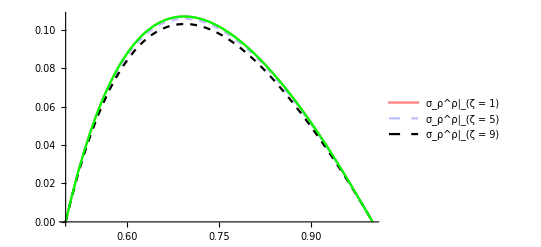

```mathematica
Plot[{(Subscript[σ, ρ]^ρ)[ρ,Subscript[ζ, 1]/5],(Subscript[σ, ρ]^ρ)[ρ,Subscript[ζ, 1]/2],(Subscript[σ, ρ]^ρ)[ρ,Subscript[ζ, 1]/1.2],(τ^n)[ρ,Subscript[ζ, 1]/5][[1,1]]},{ρ,Subscript[ρ, 0],Subscript[ρ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ρ^ρ|_(ζ = 1)","σ_ρ^ρ|_(ζ = 5)","σ_ρ^ρ|_(ζ = 9)"}]
```

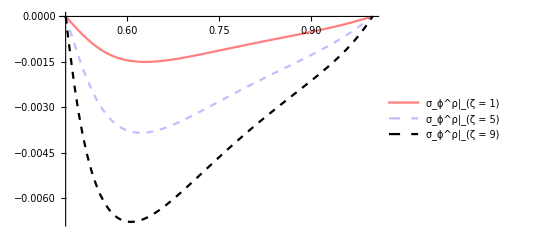

```mathematica
Plot[{(Subscript[σ, ϕ]^ρ)[ρ,Subscript[ζ, 1]/5],(Subscript[σ, ϕ]^ρ)[ρ,Subscript[ζ, 1]/2],(Subscript[σ, ϕ]^ρ)[ρ,Subscript[ζ, 1]/1.2]},{ρ,Subscript[ρ, 0],Subscript[ρ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ϕ^ρ|_(ζ = 1)","σ_ϕ^ρ|_(ζ = 5)","σ_ϕ^ρ|_(ζ = 9)"}]
```

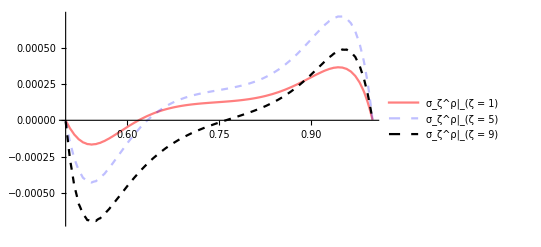

```mathematica
Plot[{(Subscript[σ, ζ]^ρ)[ρ,Subscript[ζ, 1]/5],(Subscript[σ, ζ]^ρ)[ρ,Subscript[ζ, 1]/2],(Subscript[σ, ζ]^ρ)[ρ,Subscript[ζ, 1]/1.2]},{ρ,Subscript[ρ, 0],Subscript[ρ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ζ^ρ|_(ζ = 1)","σ_ζ^ρ|_(ζ = 5)","σ_ζ^ρ|_(ζ = 9)"}]
```

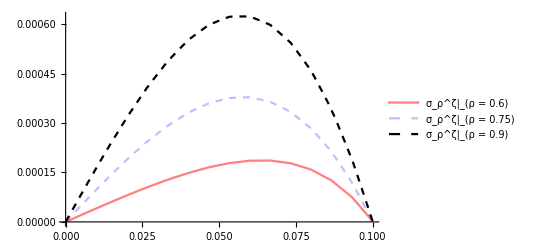

```mathematica
Plot[{(Subscript[σ, ρ]^ζ)[0.6,ζ],(Subscript[σ, ρ]^ζ)[0.75,ζ],(Subscript[σ, ρ]^ζ)[0.9,ζ]},{ζ,Subscript[ζ, 0],Subscript[ζ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ρ^ζ|_(ρ = 0.6)","σ_ρ^ζ|_(ρ = 0.75)","σ_ρ^ζ|_(ρ = 0.9)"}]
```

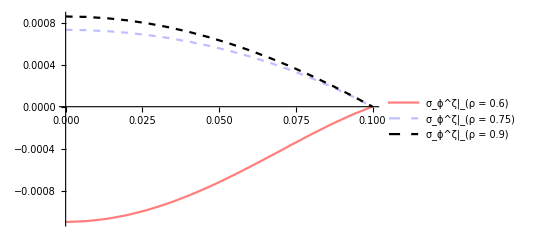

```mathematica
Plot[{(Subscript[σ, ϕ]^ζ)[0.6,ζ],(Subscript[σ, ϕ]^ζ)[0.75,ζ],(Subscript[σ, ϕ]^ζ)[0.9,ζ]},{ζ,Subscript[ζ, 0],Subscript[ζ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ϕ^ζ|_(ρ = 0.6)","σ_ϕ^ζ|_(ρ = 0.75)","σ_ϕ^ζ|_(ρ = 0.9)"}]
```

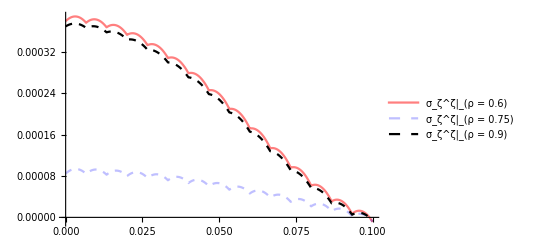

```mathematica
Plot[{(Subscript[σ, ζ]^ζ)[0.6,ζ],(Subscript[σ, ζ]^ζ)[0.75,ζ],(Subscript[σ, ζ]^ζ)[0.9,ζ]},{ζ,Subscript[ζ, 0],Subscript[ζ, 1]},PlotRange->All,PlotStyle->{{Red,Thickness->0.01,Opacity[0.5]},{Blue,Dashed,Thickness->0.01,Opacity[0.25]},{Black,Dashed,Thickness->0.01},{Green}},PlotLegends->{"σ_ζ^ζ|_(ρ = 0.6)","σ_ζ^ζ|_(ρ = 0.75)","σ_ζ^ζ|_(ρ = 0.9)"}]
```